◼ "\◼ "2024-03-27T15:08v2 .00M. J. Steil[msteil@theorie.ikp.physik.tu-darmstadt.de](mailto:msteil@theorie.ikp.physik.tu-darmstadt.de)TU Darmstadt

# I-Love-Qrot

Martin Jakob Steil^1

^1Technische Universität Darmstadt

Notebook for the computation of moments of inertia (I), tidal Love numbers (k_2), and rotational quadrupole deformations (Q) of neutron stars.
See e.g. https://arxiv.org/abs/1303.1528 for more details.

Initialization

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
$DistributedContexts={};

(* Disable Notebookhistory, [https://mathematica.stackexchange.com/questions/11258/are-there-suitable-versioning-systems-for-mathematica-notebooks]*)
SetOptions[EvaluationNotebook[],PrivateNotebookOptions->{"FileOutlineCache"->False},System`TrackCellChangeTimes->False]

(* Display the Timing of an Evaluation in a Notebook Window [https://reference.wolfram.com/language/howto/DisplayTheTimingOfAnEvaluationInANotebookWindow.html] *)
SetOptions[EvaluationNotebook[],EvaluationCompletionAction->{"ShowTiming"}]
```

#### Constants

```mathematica
c0=299792458;
G=6.67408*10^-11; 
qe=1.6021766208*10^-19;
hbar=1.054571817*10^-34;

hbarcMeVfm=hbar*c0/qe/(10^6*10^-15);

cMeVkm=G*qe/c0^4*10^3;
cfm3km3=1.*10^(18*3);
cMeVfm3km2=G*qe/c0^4*10^57; 
cMeVfm3dynecm2=1.6021766208*^33;
cMeVfm3gcm3=1.7826619069*^12;  

MS=1.9884*10^30;
MSkm=MS*G/c0^2*10^-3;
MSsymbol=Subscript["M","\[PermutationProduct]"];
```

#### Tagged Methods

```mathematica
(* SaveToCell | v2.0 | Save assigned value of symbol(s) to cell(s) | Modified Version of [http://szhorvat.net/pelican/save-data-in-notebooks.html] *)
ClearAll[SaveToCell];
SaveToCell[names_/;VectorQ[names,StringQ],suffix:Except[_?OptionQ]:"",comment:Except[_?OptionQ]:"",opt:OptionsPattern[]]:=Module[{
	data=Symbol[#]&/@names,
	label=Row[Flatten@{If[comment=!="",{Style[comment,Plain],", "},Nothing],DateString["ISODateTime"]}]
	},
	CellPrint@Cell[
		BoxData@MapThread[RowBox[{#2<>suffix,"=",ToBoxes[Iconize[#1,label,Method->Compress]],";"}]&,{data,names}],
		"Input",
		GeneratedCell->False,(*prevent deletion by Cell>Delete All Output:*)
		CellLabel->"(saved)",
		CellLabelAutoDelete->False,
		opt
	]
]

SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"",comment:Except[_?OptionQ]:"",opt:OptionsPattern[]]:=With[{
	data=Evaluate[var],
	label=Row[Flatten@{If[comment=!="",{Style[comment,Plain],", "},Nothing],DateString["ISODateTime"]}]
	},
	CellPrint@Cell[
		BoxData@RowBox[{If[name=!="",name,MakeBoxes[var]],"=",ToBoxes[Iconize[data,label,Method->Compress]],";"}],
		"Input",
		GeneratedCell->False,(*prevent deletion by Cell>Delete All Output:*)
		CellLabel->"(saved)",
		CellLabelAutoDelete->False,
		opt
	]
]
SaveToCell::usage="SaveToCell[var_,name:Except[_?OptionQ]:\"\",comment:Except[_?OptionQ]:\"\",opt:OptionsPattern[]]: saves the assignment of var/or the data in\
 var (under name if name=!=\"\") in a compressed iconized form with a label including comment and a time stamp.\n\
SaveToCell[names_/;VectorQ[names,StringQ],suffix_:Except[_?OptionQ]:\"\",comment:Except[_?OptionQ]:\"\",opt:OptionsPattern[]]: saves the assignments behind the elements of names in\
 in a compressed iconized form with suffix appended to the symbol names and a label including comment and a time stamp.";
```

```mathematica
(* AutoCollapse | v2.0 | Close CellGroup | [https://mathematica.stackexchange.com/a/683] *)
AutoCollapse[]:=Module[{},
	If[$FrontEnd=!=$Failed,
		SelectionMove[EvaluationNotebook[],All,GeneratedCell];
		FrontEndTokenExecute["SelectionCloseUnselectedCells"]
	];
]
AutoCollapse::usage="Collapse input cells by grouping them with the generated output cells.";
```

```mathematica
(* CellPrintDisplayFormulaNumbered | v2.3 | CellPrint a DisplayFormulaNumbered *)
ClearAll[CellPrintDisplayFormulaNumbered,CellPrintDisplayFormulaNumberedNAC];
CellPrintDisplayFormulaNumbered[exp_,tag_:None,comment_:"",generatedCellQ_:False,groupQ_:True,autoCollapseQ_:True]:=Module[{frameLabels,box},
	frameLabels=CellFrameLabels->{
		{None,Cell[TextData[{If[tag===None,"",ToString[tag]<>" "]<>"(",CounterBox["Chapter"],".",CounterBox["DisplayFormulaNumbered"],")"}],"DisplayFormulaEquationNumber"]},
		{None,None}
	};
	box=BoxData[RowBox[{ToBoxes[exp],RowBox[{comment}]}]];
	CellPrint[Cell[box,"DisplayFormulaNumberedPrinted",frameLabels,
		GeneratedCell->generatedCellQ,CellAutoOverwrite->True,ShowStringCharacters->False,CellGroupingRules->If[groupQ,"OutputGrouping",Inherited]]
	];
	If[autoCollapseQ,AutoCollapse[]];
]
CellPrintDisplayFormulaNumbered::usage="CellPrintDisplayFormulaNumbered[exp_,tag_:None,comment_:\"\",generatedCellQ_:False,groupQ_:True,autoCollapseQ_:True]:\
CellPrint exp to a DisplayFormulaNumberedPrinted output cell.";
CellPrintDisplayFormulaNumberedNAC[exp_,tag_:None,comment_:"",generatedCellQ_:False,groupQ_:True,autoCollapseQ_:False]:=CellPrintDisplayFormulaNumbered[exp,tag,comment,generatedCellQ,groupQ,autoCollapseQ]
CellPrintDisplayFormulaNumberedNAC::usage="Same as CellPrintDisplayFormulaNumbered[] but autoCollapseQ defaults to false.";
```

#### Notebook Style

```mathematica
plotStyle={Frame->True,FrameStyle->Directive[Thickness[0.0015]],AxesStyle->Directive[Thickness[0.0015]],ImageSize->400};

SetOptions[Plot,plotStyle];
SetOptions[LogPlot,plotStyle];
SetOptions[LogLogPlot,plotStyle];
SetOptions[ListPlot,plotStyle,PlotStyle->PointSize[0.012]];
SetOptions[ListLogPlot,plotStyle];
SetOptions[ListLogLogPlot,plotStyle];
SetOptions[ListLinePlot,plotStyle];
SetOptions[ListLogLinearPlot,plotStyle];
SetOptions[LogLinearPlot,plotStyle];


Legend[exp_,pos_:{Right,Top}]:=Placed[Style[#,FontSize->11,SingleLetterItalics->True]&/@exp,pos]
LabelText[txt_]:=Text[txt,BaseStyle->{FontSize->11}]

xDot[r_,thick___:1]:=Graphics[{AbsoluteThickness[thick],Line[{{1,1},{-1,-1}}],Line[{{-1,1},{1,-1}}]},ImageSize->r,AlignmentPoint->{0,0}]
```

General Relativity (GR) and relevant (field) equations

## GR Methods

### Partial derivatives: ∂_μ g_νκ and ∂_μ ∂_ν g_κρ

```mathematica
genMdg[Mg_,q_]:=Module[{dg,dim},
dim=Length@q;
dg=Array[
If[#1<=#2,
D[Mg[[#1,#2]],q[[#3]]]//Expand//Simplify,
Null
]&
,{dim,dim,dim}]
];
genMdg::usage = "[Mg_,q_]: Generates the symmetric components μ<=ν of the first derivative matrix (\!\(\*SubscriptBox[\(g\), \(μν, κ\)]\)). ";

genMddg[Mdg_,q_]:=Module[{ddg,dim},
dim=Length@q;
ddg=Array[
If[#3<=#4,
If[#1<=#2,
D[Mdg[[#1,#2,#3]],q[[#4]]]//Expand//Simplify,
Null],Null
]&
,{dim,dim,dim,dim}]
];
genMddg::usage = "[Mdg_,q_]: Generates the symmetric components μ<=ν and κ<=λ of the second derivative matrix (\!\(\*SubscriptBox[\(g\), \(μν, κλ\)]\)). ";

dg[Mdg_]:=Function[{i,j,k},
If[i<=j,Mdg[[i,j,k]],Mdg[[j,i,k]]]
];
dg::usage ="[Mdg_]: Access method for \!\(\*SubscriptBox[\(g\), \(μν, κ\)]\).";

ddg[Mddg_]:=Function[{i,j,k,l},
Module[{out},
If[k<=l&&i<=j,out=Mddg[[i,j,k,l]]];
If[k<=l&&i>j,out=Mddg[[j,i,k,l]]];
If[k>l&&i<=j,out=Mddg[[i,j,l,k]]];
If[k>l&&i>j,out=Mddg[[j,i,l,k]]];
out
]
];
ddg::usage ="[Mddg_]: Access method for \!\(\*SubscriptBox[\(g\), \(μν, κλ\)]\).";
```

### Christoffel symbols of the first and second kind: Γ_κμν and Γ_μν^κ

```mathematica
genΓ1[dg_,{k_,i_,j_}]:=1/2(dg[k,j,i]+dg[k,i,j]-dg[i,j,k]);
genΓ1::usage ="[dg_,{k_,i_,j_}]: Computes the Christoffel symbol of the first kind \!\(\*SubscriptBox[\(Γ\), \(κμν\)]\).";

genΓ2[MΓ1_,MgInv_,{k_,i_,j_}]:=Module[{m},Sum[MgInv[[k,m]]*MΓ1[[m,i,j]],{m,1,MΓ1//Length}]];
genΓ2::usage ="[dg_,gInv_,{k_,i_,j_}]: Computes the Christoffel symbol of the second kind \!\(\*SubsuperscriptBox[\(Γ\), \(μν\), \(κ\)]\).";

genMΓ1All[dg_,dim_:4]:=Array[If[#2<=#3,genΓ1[dg,{#1,#2,#3}],Null]&,{dim,dim,dim}];
genMΓ1All::usage = "[dg_,dim_]: Generates the symmetric components μ<=ν of the Christoffel symbols of the first kind \!\(\*SubscriptBox[\(Γ\), \(κμν\)]\).";

genMΓ2All[Γ1M_,MgInv_]:=Array[If[#2<=#3,genΓ2[Γ1M,MgInv,{#1,#2,#3}],Null]&,{MgInv//Length,MgInv//Length,MgInv//Length}];
genMΓ2All::usage = "[Γ1M_,MgInv_]: Generates the symmetric components μ<=ν of the Christoffel symbols of the second kind \!\(\*SubsuperscriptBox[\(Γ\), \(μν\), \(κ\)]\).";

Γ[ΓM_]:=Function[{k,i,j},
If[i<=j,ΓM[[k,i,j]],ΓM[[k,j,i]]]
];
Γ::usage = "[ΓM_]: Access method for the Christoffel symbols of the first \!\(\*SubscriptBox[\(Γ\), \(κμν\)]\) and second kind \!\(\*SubsuperscriptBox[\(Γ\), \(μν\), \(κ\)]\).";
```

### Covariant derivative of second rank tensors: ∇_κ T^μν

```mathematica
CoDerivativeT2[{T_,struc_},Γ2_,q_,{l_,i_,j_}]:=Module[{dim,m,der,iSum,jSum,res},
dim=Length@q;
If[MemberQ[{"uu","ud","du","dd"},struc],
der=D[T[[i,j]],q[[l]]];
If[Characters[struc][[1]]=="u",
iSum=Sum[+Γ2[i,m,l]*T[[m,j]],{m,1,dim}];,
iSum=Sum[-Γ2[m,i,l]*T[[m,j]],{m,1,dim}];
];
If[Characters[struc][[2]]=="u",
jSum=Sum[+Γ2[j,m,l]*T[[i,m]],{m,1,dim}];,
jSum=Sum[-Γ2[m,j,l]*T[[i,m]],{m,1,dim}];
];
res=der+iSum+jSum;
,(*else*)res=Null;Message[CoDerivativeT2::nnarg,struc];
];
res
]
CoDerivativeT2::nnarg="The argument `1` is not a falid tensor structure. Valid structures are 'uu', 'ud', 'du' or 'dd'.";
CoDerivativeT2::usage ="[{T_,struc_},Γ2_,q_,{l_,i_,j_}]: Computes the covariant derivative \!\(\*SubscriptBox[\(∇\), \(l\)]\)\!\(\*SuperscriptBox[\(T\), \(ij\)]\) of the second rank tensor T. Valid structures for T are 'uu', 'ud', 'du' or 'dd'.";
```

### Riemann curvature tensor: R_μνκλ

```mathematica
genRM[Mg_,{dg_,ddg_},Γ2_,{i_,k_,l_,m_}]:=Module[{dim,n,p,Rdd,RΓ1,RΓ2},
dim=Length@Mg;
Rdd=(ddg[i,m,k,l]+ddg[k,l,i,m]-ddg[i,l,k,m]-ddg[k,m,i,l]);
RΓ1=Sum[Mg[[n,p]]*Γ2[n,k,l]*Γ2[p,i,m],{n,dim},{p,dim}];
RΓ2=Sum[Mg[[n,p]]*Γ2[n,k,m]*Γ2[p,i,l],{n,dim},{p,dim}];
(1/2*Rdd+RΓ1-RΓ2)
];
genRM::usage ="[Mg_,{dg_,ddg_},Γ2_,{i_,k_,l_,m_}]: Computes a component of the Riemann curvature tensor \!\(\*SubscriptBox[\(R\), \(μνκλ\)]\).";

genMRMAll[Mg_,{dg_,ddg_},Γ2_]:=Module[{out,k,dim,dim2,syRtuples},
k=1;
dim=Length@Mg;
dim2=dim (dim-1)/2;
syRtuples=Array[Null,dim2];
Do[If[i<j,syRtuples[[k]]={i,j};k++;,Null];,{i,1,dim},{j,1,dim}];
out={syRtuples,Array[
If[#1<=#2,
genRM[Mg,{dg,ddg},Γ2,Join[syRtuples[[#1]],syRtuples[[#2]]]]
,Null]&
,{dim2,dim2}]};

out
];
genMRMAll::usage ="[Mg_,{dg_,ddg_},Γ2_]: Computes all independent components of the Riemann curvature tensor \!\(\*SubscriptBox[\(R\), \(μνκλ\)]\) 
taking the two interchange anti-symmetries and the screw symmetry into account.";

RMac[MRM_]:=Function[{i,k,l,m},
Module[{out,a,b,sign,aPos,bPos},
If[i!=k&&l!=m,
sign=1;
a=If[i<k,{i,k},sign=sign*-1;{k,i}];
b=If[l<m,{l,m},sign=sign*-1;{m,l}];
aPos=Position[MRM[[1]],a][[1,1]];
bPos=Position[MRM[[1]],b][[1,1]];
If[aPos<=bPos,
out=sign*MRM[[2]][[aPos,bPos]];,
out=sign*MRM[[2]][[bPos,aPos]];];,
out=0;
];
out]
];
RMac::usage ="[MRM_]: Access method for the Riemann curvature tensor \!\(\*SubscriptBox[\(R\), \(μνκλ\)]\).";
```

### Ricci tensor and scalar curvature: R_μν and R

```mathematica
genRicci[RM_,MgInv_,{i_,j_}]:=Module[{m,k},Sum[MgInv[[k,m]]*RM[i,k,j,m],{k,1,MgInv//Length},{m,1,MgInv//Length}]];
genRicci::usage ="[RM_,MgInv_,{i_,j_}]: Computes a component of the Ricci tensor \!\(\*SubscriptBox[\(R\), \(μν\)]\) .";

genMRicciAll[RM_,MgInv_]:=Array[If[#1<=#2,genRicci[RM,MgInv,{#1,#2}],0]&,{MgInv//Length,MgInv//Length}];
genMRicciAll::usage ="[RM_,MgInv_]: Computes all independent components of the Ricci tensor \!\(\*SubscriptBox[\(R\), \(μν\)]\) taking the interchange symmetry into account.";

Ricciac[MRicciAll_]:=Function[{i,j},
If[i<=j,MRicciAll[[i,j]],MRicciAll[[j,i]]]
];
Ricciac::usage ="[MRicciAll_]: Access method for \!\(\*SubscriptBox[\(R\), \(μν\)]\).";
```

```mathematica
R[Ricci_,MgInv_]:=Module[{i,j},
Sum[MgInv[[i,j]]*Ricci[i,j],{i,1,Length@MgInv},{j,1,Length@MgInv}]
];
R::usage ="[Ricci_,MgInv_]: Computes the scalar Curvature R.";
```

### Einstein tensor: G_μν

```mathematica
genMGAll[Ricci_,R_,Mg_]:=Array[If[#1<=#2,Ricci[#1,#2]-1/2*Mg[[#1,#2]]*R,0]&,{Mg//Length,Mg//Length}];
genMGAll::usage ="[Ricci_,R_,Mg_]: Computes all indipendent components of the Einstein Tensor \!\(\*SubscriptBox[\(G\), \(μν\)]\).";

Gac[genMGAll_]:=Function[{i,j},
If[i<=j,genMGAll[[i,j]],genMGAll[[j,i]]]
];
Gac::usage ="[genMGAll_]: Access method for \!\(\*SubscriptBox[\(G\), \(μν\)]\).";
```

### High level

```mathematica
genGR[gdd_,guu_,q_,mod_]:=Module[{t,dgM,ddgM,dgAcc,ddgAcc,ΓdddM,ΓdddAcc,ΓuddM,ΓuddAcc,RddddM,RddddAcc,RddM,RddAcc,RS,GddM,GddAcc,GudM},
t=TimeObject[];
dgM=mod[genMdg[gdd,q]];
ddgM=mod[genMddg[dgM,q]];
dgAcc=dg[dgM];
ddgAcc=ddg[ddgM];
Print["Derivatives generated in "<>ToString[TimeObject[]-t]<>"."];

t=TimeObject[];
ΓdddM=mod[genMΓ1All[dgAcc]];
ΓdddAcc=Γ[ΓdddM];
ΓuddM=mod[genMΓ2All[ΓdddM,guu]];
ΓuddAcc=Γ[ΓuddM];
Print["Christoffe symbols generated in "<>ToString[TimeObject[]-t]<>"."];

t=TimeObject[];
RddddM=mod[genMRMAll[gdd,{dgAcc,ddgAcc},ΓuddAcc]];
RddddAcc=RMac[RddddM];
Print["Riemann tensor generated in "<>ToString[TimeObject[]-t]<>"."];

t=TimeObject[];
RddM=mod[genMRicciAll[RddddAcc,guu]];
RddAcc=Ricciac[RddM];
RS=mod[R[RddAcc,guu]];
Print["Ricci tensor and scalar curvature generated in "<>ToString[TimeObject[]-t]<>"."];

t=TimeObject[];
GddM=mod[genMGAll[RddAcc,RS,gdd]];
GddAcc=Gac[GddM];
GudM=Array[Sum[guu[[#1,i]]*GddAcc[i,#2],{i,1,4}]&,{4,4}]//mod;
Print["Einstein tensor G_μν and G_ν^μ generated in "<>ToString[TimeObject[]-t]<>"."];
{ΓuddAcc,GudM}
]
```

f[x_]:=x

## Metric: Static linearized perturbations due to an external tidal field + Hartle-Thorne O[Ω^2]

(η^αβ)=diag[-1,1,1,1]; Lorentzian metric ⇒ Eastcoast-, Spacelike-Convention
dτ^2 =-dt^2+dx^2+dy^2+dz^2=-dt^2+dr^2+r^2(dθ^2+sin^2[θ] dϕ^2)=η_αβ dq^α dq^β; Flatspace Metric (r→∞)-limtit

```mathematica
$Assumptions={r>0,θ>0,θ<π,ϵ>0,ϵΩ>0,X[θ]!=0,sin[θ]∈Reals,ν[r]∈Reals,λ[r]∈Reals,P[r]>0,ρ[r]>0};
```

```mathematica
q={t,r,θ,ϕ};
exp[expression_,orderTidal_:2,orderRot_:2]:=Series[expression,{ϵ,0,orderTidal},{ϵΩ,0,orderRot}]//Normal;
```

```mathematica
g0dd=DiagonalMatrix[{-Exp[ν[r]],Exp[λ[r]],r^2,r^2sin[θ]^2}];
Row[{"g0dd=",%//MatrixForm}]//CellPrintDisplayFormulaNumbered
```

"g0dd="(-ⅇ^ν[r] | 0 | 0 | 0
0 | ⅇ^λ[r] | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 sin[θ]^2)

```mathematica
hdd=DiagonalMatrix[{Exp[ν[r]]h0[r],Exp[λ[r]]h2[r],r^2 k2[r],r^2sin[θ]^2k2[r]}]P2[θ]ϵ^2;
Row[{"hdd=",%//MatrixForm}]//CellPrintDisplayFormulaNumbered
```

"hdd="(ⅇ^ν[r] ϵ^2 h0[r] P2[θ] | 0 | 0 | 0
0 | ⅇ^λ[r] ϵ^2 h2[r] P2[θ] | 0 | 0
0 | 0 | r^2 ϵ^2 k2[r] P2[θ] | 0
0 | 0 | 0 | r^2 ϵ^2 k2[r] P2[θ] sin[θ]^2)

```mathematica
-r^2 sin[θ]^2 ω[r]ϵΩ;
fdd=SparseArray[{{1,4}->%,{4,1}->%}]//Normal;
Row[{"fdd=",%//MatrixForm}]//CellPrintDisplayFormulaNumbered
fO2dd=ϵΩ^2 DiagonalMatrix[{-Exp[ν[r]]2(h0[r]+h2[r] P2[θ])+(ω[r])^2 r^2 sin[θ]^2,2 Exp[2λ[r]]/r(m0[r]+m2[r] P2[θ]),2 r^2(v2[r]-h2[r])P2[θ],2 r^2 sin[θ]^2(v2[r]-h2[r])P2[θ]}];
Row[{"fO2dd=",%//MatrixForm}]//CellPrintDisplayFormulaNumbered
```

"fdd="(0 | 0 | 0 | -r^2 ϵΩ sin[θ]^2 ω[r]
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-r^2 ϵΩ sin[θ]^2 ω[r] | 0 | 0 | 0)

"fO2dd="(ϵΩ^2 (-2 ⅇ^ν[r] (h0[r]+h2[r] P2[θ])+r^2 sin[θ]^2 ω[r]^2) | 0 | 0 | 0
0 | (2 ⅇ^(2 λ[r]) ϵΩ^2 (m0[r]+m2[r] P2[θ]))/r | 0 | 0
0 | 0 | 2 r^2 ϵΩ^2 P2[θ] (-h2[r]+v2[r]) | 0
0 | 0 | 0 | 2 r^2 ϵΩ^2 P2[θ] sin[θ]^2 (-h2[r]+v2[r]))

Using generic function placeholders for Y20[θ] and sin[θ] avoids unnecessary trigonometric “simplifications” during intermediate steps

```mathematica
P2[θ]->LegendreP[2,Cos[θ]];
P2explicit={%,D[%,θ],D[%,θ,θ]}//Simplify
sin[θ]->Sin[θ];
sinexplicit={%,D[%,θ],D[%,θ,θ]}//Simplify
```

{P2[θ]→1/4 (1+3 Cos[2 θ]),P2'[θ]→-3 Cos[θ] Sin[θ],P2''[θ]→-3 Cos[2 θ]}

{sin[θ]→Sin[θ],sin'[θ]→Cos[θ],sin''[θ]→-Sin[θ]}

```mathematica
θl2=ArcSin[0];
θl0=ArcSin[√(2/3)]//Simplify;
```

P_2[θ_0]=0 ⇒ θ_0=ArcSin[√(2/3)]
p_2[θ_2]=1⇒ θ_2=0

Metric including tidal (T) perturbations:

```mathematica
Tgdd =g0dd+hdd;
Tguu=exp[Inverse[Tgdd]];
Tgud=exp[Array[Sum[Tguu[[#1,i]]Tgdd[[i,#2]],{i,1,4}]&,{4,4}]];
Row[{"Tguu=",%%%//MatrixForm}]//CellPrintDisplayFormulaNumbered
Row[{"Tgud=",%%%//MatrixForm}]//CellPrintDisplayFormulaNumbered
```

"Tguu="(-ⅇ^ν[r]+ⅇ^ν[r] ϵ^2 h0[r] P2[θ] | 0 | 0 | 0
0 | ⅇ^λ[r]+ⅇ^λ[r] ϵ^2 h2[r] P2[θ] | 0 | 0
0 | 0 | r^2+r^2 ϵ^2 k2[r] P2[θ] | 0
0 | 0 | 0 | r^2 sin[θ]^2+r^2 ϵ^2 k2[r] P2[θ] sin[θ]^2)

"Tgud="(-ⅇ^(-ν[r])-ⅇ^(-ν[r]) ϵ^2 h0[r] P2[θ] | 0 | 0 | 0
0 | ⅇ^(-λ[r])-ⅇ^(-λ[r]) ϵ^2 h2[r] P2[θ] | 0 | 0
0 | 0 | 1/r^2-(ϵ^2 k2[r] P2[θ])/r^2 | 0
0 | 0 | 0 | 1/(r^2 sin[θ]^2)-(ϵ^2 k2[r] P2[θ])/(r^2 sin[θ]^2))

Metric including rotational (Ω) perturbations:

```mathematica
Ωgdd =g0dd+fdd+fO2dd;
Ωguu=exp[Inverse[Ωgdd]];
Ωgud=exp[Array[Sum[Ωguu[[#1,i]]Ωgdd[[i,#2]],{i,1,4}]&,{4,4}]];
Row[{"Ωguu=",%%%//MatrixForm}]//CellPrintDisplayFormulaNumbered
Row[{"Ωgud=",%%%//MatrixForm}]//CellPrintDisplayFormulaNumbered
```

"Ωguu="(-ⅇ^ν[r]+ϵΩ^2 (-2 ⅇ^ν[r] (h0[r]+h2[r] P2[θ])+r^2 sin[θ]^2 ω[r]^2) | 0 | 0 | -r^2 ϵΩ sin[θ]^2 ω[r]
0 | ⅇ^λ[r]+(2 ⅇ^(2 λ[r]) ϵΩ^2 (m0[r]+m2[r] P2[θ]))/r | 0 | 0
0 | 0 | r^2+2 r^2 ϵΩ^2 P2[θ] (-h2[r]+v2[r]) | 0
-r^2 ϵΩ sin[θ]^2 ω[r] | 0 | 0 | r^2 sin[θ]^2+2 r^2 ϵΩ^2 P2[θ] sin[θ]^2 (-h2[r]+v2[r]))

"Ωgud="(-ⅇ^(-ν[r])+2 ⅇ^(-ν[r]) ϵΩ^2 (h0[r]+h2[r] P2[θ]) | 0 | 0 | -ⅇ^(-ν[r]) ϵΩ ω[r]
0 | ⅇ^(-λ[r])-(2 ϵΩ^2 (m0[r]+m2[r] P2[θ]))/r | 0 | 0
0 | 0 | 1/r^2+(ϵΩ^2 (2 h2[r] P2[θ]-2 P2[θ] v2[r]))/r^2 | 0
-ⅇ^(-ν[r]) ϵΩ ω[r] | 0 | 0 | 1/(r^2 sin[θ]^2)-(ⅇ^(-ν[r]) ϵΩ^2 (-2 ⅇ^ν[r] h2[r] P2[θ]+2 ⅇ^ν[r] P2[θ] v2[r]+r^2 sin[θ]^2 ω[r]^2))/(r^2 sin[θ]^2))

### Compute Einstein tensor G_ν^μ using GR Methods

Derivatives generated in 0.115946 seconds.

Christoffe symbols generated in 0.0312141 seconds.

Riemann tensor generated in 0.115898 seconds.

Ricci tensor and scalar curvature generated in 0.269618 seconds.

Einstein tensor G_μν and G_ν^μ generated in 0.216295 seconds.

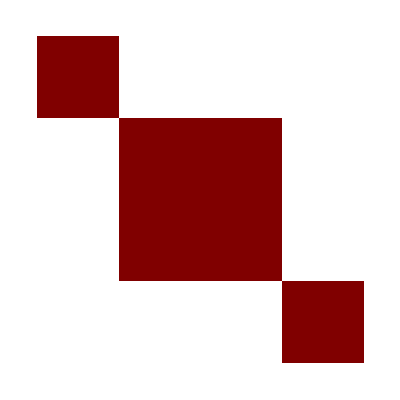

```mathematica
{TΓudd,TGud}=genGR[Tgdd,Tguu,q,exp];
TGud//ArrayPlot
```

Derivatives generated in 0.512335 seconds.

Christoffe symbols generated in 0.0820061 seconds.

Riemann tensor generated in 0.327116 seconds.

Ricci tensor and scalar curvature generated in 0.461845 seconds.

Einstein tensor G_μν and G_ν^μ generated in 0.374657 seconds.

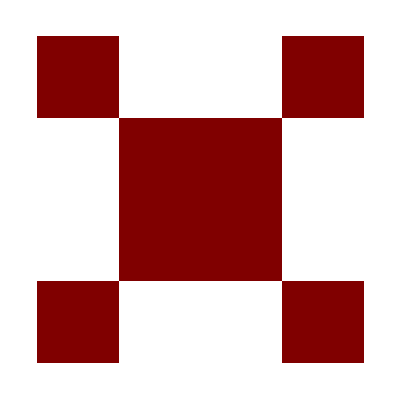

```mathematica
{ΩΓudd,ΩGud}=genGR[Ωgdd,Ωguu,q,exp];
ΩGud//ArrayPlot
```

## Source Terms T_μν: perturbed ideal fluid

((T̄)^αβ)=diag[ϵ,p,p,p], Restframe ideal fluid
T^αβ=p g^αβ+(p+ϵ)u^α u^β, Comoving fluid frame
T_β^α=p g_β^α+(p+ϵ)u^α u_β

u^ϕ≡dϕ/dτ=dϕ/dτ dt/dt=dϕ/dt dt/dτ=Ω u^t
u^r=u^θ=0, da v^r=v^θ=0

v⃗≡(d r⃗)/dt
γ≡1/(√(1-(v⃗)^2))
dτ=dt/γ
u^α≡dq^α/dτ=γ(1,v^1,v^2,v^3)
u_α=γ(-1,v^1,v^2,v^3)
u_α u^α=-1, Lorentz scalar

u_α u^α=-1=u_t u^t+u_ϕ u^ϕ=u^t g_tm u^m+u^ϕ g_ϕm u^m=u^t(g_tt u^t+g_tϕ u^ϕ)+u^ϕ(g_ϕt u^t+g_ϕϕ u^ϕ)
-1=(u^t)^2+2 u^t u^ϕ g_tϕ+(u^ϕ)^2 g_ϕϕ=(u^t)^2(g_tt+2 g_tϕ Ω+g_ϕϕ Ω^2)

u^t=1/(√(-(g_tt+2 g_tϕ Ω+g_ϕϕ Ω^2)))=ⅇ^(-ν[r]/2)+O[Ω]^2
u^ϕ=Ω u^t=Ωⅇ^(-ν[r]/2)

```mathematica
TVu=exp[{1,0,0,0}/Sqrt[-(Tgdd[[1,1]])],2,2]//FullSimplify
ΩVu=exp[{1,0,0,ϵΩ Ω}/Sqrt[-(Ωgdd[[1,1]]+2 ϵΩ Ω Ωgdd[[1,4]]+ϵΩ^2 Ω^2 Ωgdd[[4,4]])],2,2]//FullSimplify
```

{1/2 ⅇ^(-ν[r]/2) (2+ϵ^2 h0[r] P2[θ]),0,0,0}

{1/2 ⅇ^(-(3 ν[r])/2) (-2 ⅇ^ν[r] (-1+ϵΩ^2 (h0[r]+h2[r] P2[θ]))+r^2 ϵΩ^2 sin[θ]^2 (Ω-ω[r])^2),0,0,ⅇ^(-ν[r]/2) ϵΩ Ω}

```mathematica
TVd=exp[TVu.Tgdd,2,2]//FullSimplify
ΩVd=exp[ΩVu.Ωgdd,2,2]//FullSimplify
```

{1/2 ⅇ^(ν[r]/2) (-2+ϵ^2 h0[r] P2[θ]),0,0,0}

{1/2 ⅇ^(-ν[r]/2) (-2 ⅇ^ν[r] (1+ϵΩ^2 (h0[r]+h2[r] P2[θ]))+r^2 ϵΩ^2 sin[θ]^2 (-Ω^2+ω[r]^2)),0,0,ⅇ^(-ν[r]/2) r^2 ϵΩ sin[θ]^2 (Ω-ω[r])}

```mathematica
TVd.TVu//Simplify
ΩVd.ΩVu//Simplify
```

-1+1/4 ϵ^4 h0[r]^2 P2[θ]^2

1/4 ⅇ^(-2 ν[r]) (4 ⅇ^ν[r] r^2 ϵΩ^2 Ω sin[θ]^2 (Ω-ω[r])+(-2 ⅇ^ν[r] (-1+ϵΩ^2 (h0[r]+h2[r] P2[θ]))+r^2 ϵΩ^2 sin[θ]^2 (Ω-ω[r])^2) (-2 ⅇ^ν[r] (1+ϵΩ^2 (h0[r]+h2[r] P2[θ]))+r^2 ϵΩ^2 sin[θ]^2 (-Ω^2+ω[r]^2)))

Energy-Momentum tensor perturbations:δρ[r,θ] and  δP[r,θ];
δρ[r,θ]=dρ[r]/dP[r]δP[r,θ]+O[ϵ^3] with the EOS

```mathematica
ΔP=δP[r,θ] ϵ^2+ϵΩ^2(ρ[r]+P[r])(p0[r]+p2[r] P2[θ]);
Δρ=dρdP[P[r]](ΔP);
TTud=exp[Array[(ρ[r]+Δρ+P[r]+ΔP)TVu[[#1]]TVd[[#2]]+(P[r]+ΔP)Tgud[[#1,#2]]&,{4,4}],2,0];
Row[{"TTud=",%//MatrixForm}]//CellPrintDisplayFormulaNumbered
ΩTud=exp[Array[(ρ[r]+Δρ+P[r]+ΔP)ΩVu[[#1]]ΩVd[[#2]]+(P[r]+ΔP)Ωgud[[#1,#2]]&,{4,4}],0,2];
Row[{"ΩTud=",%//MatrixForm}]//CellPrintDisplayFormulaNumbered
```

"TTud="(-ϵ^2 dρdP[P[r]] δP[r,θ]-ρ[r] | 0 | 0 | 0
0 | P[r]+ϵ^2 δP[r,θ] | 0 | 0
0 | 0 | P[r]+ϵ^2 δP[r,θ] | 0
0 | 0 | 0 | P[r]+ϵ^2 δP[r,θ])

"ΩTud="(-ρ[r]-ⅇ^(-ν[r]) ϵΩ^2 (P[r]+ρ[r]) (ⅇ^ν[r] dρdP[P[r]] p0[r]+ⅇ^ν[r] dρdP[P[r]] p2[r] P2[θ]+r^2 Ω^2 sin[θ]^2-r^2 Ω sin[θ]^2 ω[r]) | 0 | 0 | ⅇ^(-ν[r]) r^2 ϵΩ sin[θ]^2 (P[r]+ρ[r]) (Ω-ω[r])
0 | P[r]+ϵΩ^2 (p0[r]+p2[r] P2[θ]) (P[r]+ρ[r]) | 0 | 0
0 | 0 | P[r]+ϵΩ^2 (p0[r]+p2[r] P2[θ]) (P[r]+ρ[r]) | 0
-ϵΩ Ω (P[r]+ρ[r]) | 0 | 0 | P[r]+ϵΩ^2 ((p0[r]+p2[r] P2[θ]) (P[r]+ρ[r])+ⅇ^(-ν[r]) r^2 Ω sin[θ]^2 (P[r]+ρ[r]) (Ω-ω[r])))

```mathematica
ΩTuu=exp[Array[(ρ[r]+Δρ+P[r]+ΔP)ΩVu[[#1]]ΩVu[[#2]]+(P[r]+ΔP)Ωguu[[#1,#2]]&,{4,4}],0,2];
```

## Field equations

### O[ϵ^0]: TOV equations → Non-perturbed background star

```mathematica
FE00ud=exp[TGud-8π*TTud,0,0]/.sinexplicit//Simplify;
Row[{"G_ν^μ-8πT_ν^μ=",%//MatrixForm,"+O[ϵ^2]"}]//CellPrintDisplayFormulaNumbered
```

"G_ν^μ-8πT_ν^μ="(8 π ρ[r]-(ⅇ^(-λ[r]) (-1+ⅇ^λ[r]+r λ'[r]))/r^2 | 0 | 0 | 0
0 | (-1+ⅇ^(-λ[r])-8 π r^2 P[r]+ⅇ^(-λ[r]) r ν'[r])/r^2 | 0 | 0
0 | 0 | (ⅇ^(-λ[r]) (-32 ⅇ^λ[r] π r P[r]+2 ν'[r]+r ν'[r]^2-λ'[r] (2+r ν'[r])+2 r ν''[r]))/(4 r) | 0
0 | 0 | 0 | (ⅇ^(-λ[r]) (-32 ⅇ^λ[r] π r P[r]+2 ν'[r]+r ν'[r]^2-λ'[r] (2+r ν'[r])+2 r ν''[r]))/(4 r))"+O[ϵ^2]"

Using the mixed tensor version of the field equations simplifies the involved differential equations

#### λ[r] - M[r] - Relation

G_11-8π T_11=0
⇒-1+ⅇ^(-λ[r])+8 π r^2 ρ[r]-ⅇ^(-λ[r]) r λ'[r]==0
⇔-1+ⅇ^(-λ[r])-ⅇ^(-λ[r]) r λ'[r]==-8 π r^2 ρ[r]≡-2M'[r], with M'[r]≡4 π r^2 ρ[r]
⇔d/dr(rⅇ^(-λ[r])-r)==-2M'[r]
⇒ⅇ^(-λ[r])==1-(2M[r])/r
⇔ⅇ^λ[r]==(1-(2M[r])/r)^-1

```mathematica
FE00ud[[1,1]]==0//Simplify
```

1+8 ⅇ^λ[r] π r^2 ρ[r]==ⅇ^λ[r]+r λ'[r]

```mathematica
Solve[Integrate[-1+ⅇ^(-λ[r])-ⅇ^(-λ[r]) r λ'[r],r]==-2M[r]//.{ⅇ^(- λ[r])->1/x[r],ⅇ^λ[r]->x[r]},x[r]][[1]]//.x[r]->ⅇ^λ[r]
```

{ⅇ^λ[r]→r/(r-2 M[r])}

```mathematica
λMrules={λ[r]->Log[r/(r-2 M[r])],λ'[r]->(2 (-M[r]+r M'[r]))/(r (r-2 M[r]))};
dMdrRule=M'[r]->4 π r^2 ρ[r];
Mλrule=M[r]->1/2 ⅇ^(-λ[r]) (-1+ⅇ^λ[r]) r;
```

#### TOV equation(s)

```mathematica
Div00Tuu=exp[Array[Sum[CoDerivativeT2[{ΩTuu,"uu"},TΓudd,q,{m,#1,m}],{m,1,4}]&,4],0,0]//Simplify;
Row[{"∇_μ T^νμ=",%//MatrixForm,"+O[ϵ^2]"}]//CellPrintDisplayFormulaNumbered
```

"∇_μ T^νμ="(0
1/2 ⅇ^(-λ[r]) (2 P'[r]+(P[r]+ρ[r]) ν'[r])
0
0)"+O[ϵ^2]"

Using the energy conservation equation is not necessary but it simplifies the derivation of the TOV equation and is in close analogy to the classical derivation of the equation of hydrostatic equilibrium

TOV equations in terms of metric potentials

```mathematica
tovEqs=Solve[{FE00ud[[1,1]]==0,FE00ud[[2,2]]==0,Div00Tuu[[2]]==0},{P'[r],λ'[r],ν'[r]}][[1]]//Simplify;
%//Column//CellPrintDisplayFormulaNumbered
```

P'[r]→-((-1+ⅇ^λ[r]+8 ⅇ^λ[r] π r^2 P[r]) (P[r]+ρ[r]))/(2 r)
λ'[r]→(1-ⅇ^λ[r]+8 ⅇ^λ[r] π r^2 ρ[r])/r
ν'[r]→(-1+ⅇ^λ[r]+8 ⅇ^λ[r] π r^2 P[r])/r

```mathematica
Solve[{ν'[r]==(ν'[r]/.tovEqs),λ'[r]==(λ'[r]/.tovEqs)},{P[r],ρ[r]},Assumptions->r>0][[1]];
tovEqsPρ=Join[%,D[%,r]]//Simplify;
%//Column//CellPrintDisplayFormulaNumbered
```

P[r]→(ⅇ^(-λ[r]) (1-ⅇ^λ[r]+r ν'[r]))/(8 π r^2)
ρ[r]→(ⅇ^(-λ[r]) (-1+ⅇ^λ[r]+r λ'[r]))/(8 π r^2)
P'[r]→(ⅇ^(-λ[r]) (-2+2 ⅇ^λ[r]-r ν'[r]-r λ'[r] (1+r ν'[r])+r^2 ν''[r]))/(8 π r^3)
ρ'[r]→(ⅇ^(-λ[r]) (2-2 ⅇ^λ[r]-r^2 λ'[r]^2+r^2 λ''[r]))/(8 π r^3)

Common form of the TOV equations

```mathematica
tovEqsCanonical={tovEqs[[1]],dMdrRule,tovEqs[[3]]}/.λMrules//Simplify;
ν'[r]->(%[[3,2]]/P'[r]/.%[[1]]//Simplify)P'[r];
{%%[[1]],%%[[2]],%}//Column//CellPrintDisplayFormulaNumbered
```

P'[r]→-((M[r]+4 π r^3 P[r]) (P[r]+ρ[r]))/(r (r-2 M[r]))
M'[r]→4 π r^2 ρ[r]
ν'[r]→-(2 P'[r])/(P[r]+ρ[r])

Interior Schwarzschild Solution ρ=const.

```mathematica
M[r]->4/3 π r^3 ρc;
{ρ[r]->ρc,%,D[%,r]};
tovEqsCanonical/.%//Simplify
DSolve[{%[[1]]/.Rule->Equal},P[r],r]//Simplify//First;
%/.First@Solve[0==P[r]/.%/.r->R,C[1]]/.C[2]->0//Simplify
First@Simplify[%/.ρc->(3 Z)/(4 π R^2),Assumptions->{r>0,R>0,r<R}]
ISSPofr={%,D[%,r]}//Simplify
```

{P'[r]→(4 π r (ρc+P[r]) (ρc+3 P[r]))/(-3+8 π r^2 ρc),4 π r^2 ρc→4 π r^2 ρc,ν'[r]→-(8 π r (ρc+3 P[r]))/(-3+8 π r^2 ρc)}

{P[r]→(ρc (-√(-3+8 π r^2 ρc)+√(-3+8 π R^2 ρc)))/(√(-3+8 π r^2 ρc)-3 √(-3+8 π R^2 ρc))}

P[r]→(3 Z (√(-3+6 Z)-√(-3+(6 r^2 Z)/R^2)))/(4 π R^2 (-3 √(-3+6 Z)+√(-3+(6 r^2 Z)/R^2)))

{P[r]→(3 Z (√(-3+6 Z)-√(-3+(6 r^2 Z)/R^2)))/(4 π R^2 (-3 √(-3+6 Z)+√(-3+(6 r^2 Z)/R^2))),P'[r]→(3 r Z^2 √(-1+2 Z))/(π R^4 √(-1+(2 r^2 Z)/R^2) (-3 √(-1+2 Z)+√(-1+(2 r^2 Z)/R^2))^2)}

```mathematica
{M[r]->(r^3 Z)/R^2,M'[r]->3(r^2 Z)/R^2,ρ[r]->(3 Z)/(4 π R^2)};
Join[%,λMrules/.%//Simplify];
tovEqs/.%//Simplify;
%/.ISSPofr//Simplify;
ISSrules={%%%,ISSPofr,%[[3]],D[%[[3]],r]}//Simplify//Flatten
```

{M[r]→(r^3 Z)/R^2,M'[r]→(3 r^2 Z)/R^2,ρ[r]→(3 Z)/(4 π R^2),λ[r]→Log[R^2/(R^2-2 r^2 Z)],λ'[r]→(4 r Z)/(R^2-2 r^2 Z),P[r]→(3 Z (√(-3+6 Z)-√(-3+(6 r^2 Z)/R^2)))/(4 π R^2 (-3 √(-3+6 Z)+√(-3+(6 r^2 Z)/R^2))),P'[r]→(3 r Z^2 √(-1+2 Z))/(π R^4 √(-1+(2 r^2 Z)/R^2) (-3 √(-1+2 Z)+√(-1+(2 r^2 Z)/R^2))^2),ν'[r]→(4 r Z √(-1+(2 r^2 Z)/R^2))/((-R^2+2 r^2 Z) (-3 √(-1+2 Z)+√(-1+(2 r^2 Z)/R^2))),ν''[r]→(4 Z (-4 r^4 Z^2+R^4 (1+3 √(-1+2 Z) √(-1+(2 r^2 Z)/R^2))))/(R^2 (R^2-2 r^2 Z)^2 (-3 √(-1+2 Z)+√(-1+(2 r^2 Z)/R^2))^2)}

```mathematica
ISSrules;
ISSrulesSeries=#[[1]]->Series[#[[2]],{Z,0,4},Assumptions->{Z>0,r>0,R>0,r<R}]&/@%
```

{M[r]→(r^3 Z)/R^2+O[Z]^5,M'[r]→(3 r^2 Z)/R^2+O[Z]^5,ρ[r]→(3 Z)/(4 π R^2)+O[Z]^5,λ[r]→(2 r^2 Z)/R^2+(2 r^4 Z^2)/R^4+(8 r^6 Z^3)/(3 R^6)+(4 r^8 Z^4)/R^8+O[Z]^5,λ'[r]→(4 r Z)/R^2+(8 r^3 Z^2)/R^4+(16 r^5 Z^3)/R^6+(32 r^7 Z^4)/R^8+O[Z]^5,P[r]→-(3 (r^2-R^2) Z^2)/(8 (π R^4))+(3 (-r^2+R^2) Z^3)/(4 π R^4)+(3 (-r^6+3 r^4 R^2-19 r^2 R^4+17 R^6) Z^4)/(32 π R^8)+O[Z]^5,P'[r]→-(3 r Z^2)/(4 (π R^4))-(3 r Z^3)/(2 (π R^4))-(3 (r (3 r^4-6 r^2 R^2+19 R^4)) Z^4)/(16 (π R^8))+O[Z]^5,ν'[r]→(2 r Z)/R^2+(r (r^2+3 R^2) Z^2)/R^4+(2 r (r^4+3 R^4) Z^3)/R^6+(r (13 r^6+9 r^4 R^2-9 r^2 R^4+51 R^6) Z^4)/(4 R^8)+O[Z]^5,ν''[r]→(2 Z)/R^2+(3 (r^2+R^2) Z^2)/R^4+(2 (5 r^4+3 R^4) Z^3)/R^6+((91 r^6+45 r^4 R^2-27 r^2 R^4+51 R^6) Z^4)/(4 R^8)+O[Z]^5}

### O[ϵΩ^1]: HT frame-dragging equation ω’’[r] → moment of inertia I

```mathematica
ωbarRule={ω[r]->Ω-ωbar[r],ω'[r]->-ωbar'[r],ω''[r]->-ωbar''[r]};
ωRule={ωbar[r]->Ω-ω[r],ωbar'[r]->-ω'[r],ωbar''[r]->-ω''[r]};
```

```mathematica
FE01ud=exp[ΩGud-8π*ΩTud,0,1]-FE00ud//Simplify;
Row[{"FE01ud=",FE01ud//.sinexplicit//MatrixForm}]//CellPrintDisplayFormulaNumbered
```

"FE01ud="(0 | 0 | 0 | 1/4 ⅇ^(-ν[r]) r ϵΩ Sin[θ]^2 (-32 π r (P[r]+ρ[r]) (Ω-ω[r])+ⅇ^(-λ[r]) ((-8+r λ'[r]+r ν'[r]) ω'[r]-2 r ω''[r]))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
8 π ϵΩ Ω P[r]-(ϵΩ ω[r])/r^2+(ⅇ^(-λ[r]) ϵΩ (32 ⅇ^λ[r] π r^2 Ω ρ[r]+ω[r] (4-2 r ν'[r]-r^2 ν'[r]^2+r λ'[r] (-2+r ν'[r])-2 r^2 ν''[r])-r ((-8+r λ'[r]+r ν'[r]) ω'[r]-2 r ω''[r])))/(4 r^2) | 0 | 0 | 0)

```mathematica
FE01ud[[1,4]];
Row[{"G_ϕ^t-8πT_ϕ^t=",%//MatrixForm,"+O[ϵΩ^2]"}]//CellPrintDisplayFormulaNumbered
Solve[0==%%/.sinexplicit/.ωbarRule/.tovEqsPρ,ωbar''[r]]//Simplify;
ωbar''[r]-(ωbar''[r]/.%);
ωbarODE=0==Coefficient[%,ωbar''[r]][[1]]ωbar''[r]+Simplify[Coefficient[%,ωbar'[r]][[1]]]ωbar'[r]+Simplify[Coefficient[%,ωbar[r]][[1]]]ωbar[r];
ωbarODEvec={Coefficient[%%,ωbar''[r]][[1]],Simplify[Coefficient[%%,ωbar'[r]][[1]]],Simplify[Coefficient[%%,ωbar[r]][[1]]]};
ωbarODE//CellPrintDisplayFormulaNumbered
```

"G_ϕ^t-8πT_ϕ^t="1/4 ⅇ^(-ν[r]) r ϵΩ sin[θ]^2 (-32 π r (P[r]+ρ[r]) (Ω-ω[r])+ⅇ^(-λ[r]) ((-8+r λ'[r]+r ν'[r]) ω'[r]-2 r ω''[r]))"+O[ϵΩ^2]"

0==-(2 ωbar[r] (λ'[r]+ν'[r]))/r-((-8+r λ'[r]+r ν'[r]) ωbar'[r])/(2 r)+ωbar''[r]

```mathematica
ωbarODErule=Solve[ωbarODE,ωbar''[r]][[1]];
```

### O[ϵΩ^2]: Rotational deformation → rotational quadrupole moment Q

```mathematica
FE02ud=(exp[ΩGud-8π*ΩTud,0,2])//Expand;
```

```mathematica
exp[Sum[CoDerivativeT2[{ΩTuu,"uu"},ΩΓudd,q,{m,3,m}],{m,1,4}],0,2]-Div00Tuu[[3]]//Simplify;
Divθ02Tuu=%/.P2explicit/.sinexplicit/.ωbarRule//Simplify
```

-1/r^2 ⅇ^(-ν[r]) ϵΩ^2 Cos[θ] Sin[θ] (P[r]+ρ[r]) (3 ⅇ^ν[r] h2[r]+3 ⅇ^ν[r] p2[r]+r^2 ωbar[r]^2)

```mathematica
eq02ud3344=FE02ud[[3,3]]-FE02ud[[4,4]]/.P2explicit/.sinexplicit/.ωbarRule/.ωbarODErule/.tovEqs//Simplify
```

-1/(2 r^3)ⅇ^(-λ[r]-ν[r]) ϵΩ^2 Sin[θ]^2 (6 ⅇ^(λ[r]+ν[r]) r h2[r]+6 ⅇ^(2 λ[r]+ν[r]) m2[r]-r^5 (16 ⅇ^λ[r] π P[r] ωbar[r]^2+16 ⅇ^λ[r] π ρ[r] ωbar[r]^2+ωbar'[r]^2))

```mathematica
eq02u2d3=FE02ud[[2,3]]/.P2explicit//Simplify
```

1/(2 r^2)3 ⅇ^(-λ[r]) ϵΩ^2 Cos[θ] Sin[θ] (2 r^2 v2'[r]+r h2[r] (-2+r ν'[r])-ⅇ^λ[r] m2[r] (2+r ν'[r]))

```mathematica
TrigExpand[FE02ud[[2,2]]]/.ωbarRule/.ωbarODErule/.tovEqs/.P2explicit/.sinexplicit;
%/.θ->θl0//Simplify;
eq02ud22L2=(%%/.θ->θl2)-%//Simplify
```

1/(6 r^3)ϵΩ^2 (-12 r h2[r]-12 ⅇ^λ[r] m2[r] (1+8 π r^2 P[r])-24 r v2[r]-48 π r^3 P[r] (p2[r]+r (h2'[r]-v2'[r]))+r^2 (-48 π r p2[r] ρ[r]+(-6+6 ⅇ^(-λ[r])) h2'[r]+6 v2'[r]+6 ⅇ^(-λ[r]) v2'[r]-ⅇ^(-λ[r]-ν[r]) r^3 ωbar'[r]^2))

```mathematica
O02odes=Solve[{0==Divθ02Tuu,0==eq02u2d3,0==eq02ud3344,0==eq02ud22L2},{m2[r],p2[r],v2'[r],h2'[r]},Assumptions->r>0][[1]];
O02odes/.tovEqsPρ//Simplify//Expand//Column//CellPrintDisplayFormulaNumbered
```

m2[r]→-ⅇ^(-λ[r]) r h2[r]+1/3 ⅇ^(-2 λ[r]-ν[r]) r^4 ωbar[r]^2 λ'[r]+1/3 ⅇ^(-2 λ[r]-ν[r]) r^4 ωbar[r]^2 ν'[r]+1/6 ⅇ^(-2 λ[r]-ν[r]) r^5 ωbar'[r]^2
p2[r]→-h2[r]-1/3 ⅇ^(-ν[r]) r^2 ωbar[r]^2
v2'[r]→1/3 ⅇ^(-λ[r]-ν[r]) r^2 ωbar[r]^2 λ'[r]-h2[r] ν'[r]+1/3 ⅇ^(-λ[r]-ν[r]) r^2 ωbar[r]^2 ν'[r]+1/6 ⅇ^(-λ[r]-ν[r]) r^3 ωbar[r]^2 λ'[r] ν'[r]+1/6 ⅇ^(-λ[r]-ν[r]) r^3 ωbar[r]^2 ν'[r]^2+1/6 ⅇ^(-λ[r]-ν[r]) r^3 ωbar'[r]^2+1/12 ⅇ^(-λ[r]-ν[r]) r^4 ν'[r] ωbar'[r]^2
h2'[r]→h2[r]/r+1/3 ⅇ^(-ν[r]) r ωbar[r]^2+(2 h2[r])/(r^2 ν'[r])-(2 ⅇ^λ[r] h2[r])/(r^2 ν'[r])-(4 ⅇ^λ[r] v2[r])/(r^2 ν'[r])+(h2[r] λ'[r])/(r ν'[r])+(ⅇ^(-ν[r]) r ωbar[r]^2 λ'[r])/(3 ν'[r])-h2[r] ν'[r]+1/6 ⅇ^(-λ[r]-ν[r]) r^3 ωbar[r]^2 λ'[r] ν'[r]+1/6 ⅇ^(-λ[r]-ν[r]) r^3 ωbar[r]^2 ν'[r]^2-(ⅇ^(-ν[r]) r^2 ωbar'[r]^2)/(6 ν'[r])+1/12 ⅇ^(-λ[r]-ν[r]) r^4 ν'[r] ωbar'[r]^2

```mathematica
O02odes[[3;;4]]/.{ωbar[r]->0,ωbar'[r]->0}/.λMrules//Simplify;
v2h2HODE=%/.{h2[r] ->h2H[r],v2[r]->v2H[r]}/.D[{h2[r] ->h2H[r],v2[r]->v2H[r]},r]//FullSimplify;
v2h2PODE=O02odes[[3;;4]]/.λMrules/.{h2[r] ->h2P[r],v2[r]->v2P[r]}/.D[{h2[r] ->h2P[r],v2[r]->v2P[r]},r]//Simplify;
```

```mathematica
v2h2HODE//Column//CellPrintDisplayFormulaNumbered
v2h2PODE//Column//CellPrintDisplayFormulaNumbered
```

v2H'[r]→-h2H[r] ν'[r]
h2H'[r]→(-2 v2H[r]+h2H[r] (4 π r^2 (3 P[r]+ρ[r])+(-r+M[r]-4 π r^3 P[r]) ν'[r]))/(M[r]+4 π r^3 P[r])

v2P'[r]→1/12 ⅇ^(-ν[r]) (-12 ⅇ^ν[r] h2P[r] ν'[r]+16 π r^3 P[r] ωbar[r]^2 (2+r ν'[r])+16 π r^3 ρ[r] ωbar[r]^2 (2+r ν'[r])+2 r^3 ωbar'[r]^2-4 r^2 M[r] ωbar'[r]^2+r^4 ν'[r] ωbar'[r]^2-2 r^3 M[r] ν'[r] ωbar'[r]^2)
h2P'[r]→1/(12 (M[r]+4 π r^3 P[r]))ⅇ^(-ν[r]) (-24 ⅇ^ν[r] v2P[r]-12 ⅇ^ν[r] h2P[r] (-4 π r^2 ρ[r]+(r-M[r]) ν'[r]+4 π r^2 P[r] (-3+r ν'[r]))+r^2 (64 π^2 r^4 P[r]^2 ωbar[r]^2 (-2+r ν'[r])+16 π r ρ[r] ωbar[r]^2 (r (1+r ν'[r])-M[r] (2+r ν'[r]))+(r-2 M[r]) (r (-1+r ν'[r])-M[r] (2+r ν'[r])) ωbar'[r]^2+4 π r P[r] (4 ωbar[r]^2 (r+r^2 ν'[r]+4 π r^3 ρ[r] (-2+r ν'[r])-M[r] (2+r ν'[r]))+r^2 (r-2 M[r]) (-2+r ν'[r]) ωbar'[r]^2)))

```mathematica
v2h2HODE[[1]]/.ν'[r]->(2 M[r]+8 π r^3 P[r])/(r^2-2 r M[r]);
Collect[%,{ωbar[r]^2,ωbar'[r]^2,h2H[r],v2H[r]},Simplify]
%/.{P[r]->Pr[r],ρ[r]->ρofp[Pr[r]],M[r]->Mr[r],ν[r]->νr[r],ωbar[r]->ωbarr[r],ωbar'[r]->dωbarr[r]}
```

v2H'[r]→-(2 h2H[r] (M[r]+4 π r^3 P[r]))/(r (r-2 M[r]))

v2H'[r]→-(2 h2H[r] (Mr[r]+4 π r^3 Pr[r]))/(r (r-2 Mr[r]))

```mathematica
v2h2PODE={v2h2PODE[[1,1]]->Collect[v2h2PODE[[1,2]],{h2P[r] ,v2P[r],ωbar[r]^2 ,ωbar'[r]^2},Simplify],v2h2PODE[[2,1]]->Collect[v2h2PODE[[2,2]],{h2P[r] ,v2P[r],ωbar[r]^2 ,ωbar'[r]^2},Simplify]};
```

### O[ϵ^2]: Linearized tidal perturbations equation h0’’[r] → tidal love number k_2

Derivation due to [Tanja Hinderer, 2008, TIDAL LOVE NUMBERS OF NEUTRON STARS, APJ  677:1216Y1220]

```mathematica
FE20ud=exp[TGud-8π*TTud,2,0]-FE00ud;
```

```mathematica
exp[FE20ud[[3,3]]-FE20ud[[4,4]]]/.P2explicit/.sinexplicit//Simplify;
Row[{"0=FE_θ^θ-FE_ϕ^ϕ=",%/.ϵ->1,"+O[ϵ^3] ⇔ ",h2[r]->h0[r]}]//CellPrintDisplayFormulaNumbered
%%/.P2explicit//Simplify;
Solve[0==%,h2[r]][[1,1]];
h2rule={%,D[%,r],D[%,r,r]};
```

"0=FE_θ^θ-FE_ϕ^ϕ="(3 (h0[r]-h2[r]) Sin[θ]^2)/(2 r^2)"+O[ϵ^3] ⇔ "h2[r]→h0[r]

```mathematica
FE20ud[[2,3]]/.h2rule/.P2explicit/.sinexplicit//Simplify;
Solve[Reduce[%==0,k2'[r]][[-1]],k2'[r]][[1,1]];
Row[{"0=FE_θ^r=",%%/.ϵ->1,"+O[ϵ^3] ⇔ ",%}]//CellPrintDisplayFormulaNumbered
k2rule={%%,D[%%,r]};
```

"0=FE_θ^r="-3/4 ⅇ^(-λ[r]) Sin[2 θ] (h0'[r]-k2'[r]+h0[r] ν'[r])"+O[ϵ^3] ⇔ "k2'[r]→h0'[r]+h0[r] ν'[r]

```mathematica
FE20ud[[3,3]]+FE20ud[[4,4]]/.h2rule/.k2rule/.sinexplicit//Simplify;
δPrule=Solve[%==0,δP[r,θ]][[1,1]]//Simplify;
Row[{"0=FE_θ^θ+FE_ϕ^ϕ=",%%/.ϵ->1,"+O[ϵ^3] ⇔ ",%}]//CellPrintDisplayFormulaNumbered
```

"0=FE_θ^θ+FE_ϕ^ϕ="-16 π δP[r,θ]+(ⅇ^(-λ[r]) h0[r] P2[θ] (λ'[r]+ν'[r]))/r"+O[ϵ^3] ⇔ "δP[r,θ]→(ⅇ^(-λ[r]) h0[r] P2[θ] (λ'[r]+ν'[r]))/(16 π r)

```mathematica
FE20ud[[1,1]]-FE20ud[[2,2]]/.k2rule/.h2rule/.δPrule/.P2explicit/.sinexplicit//Simplify;
ddhODE=%/.Solve[FE00ud[[3,3]]==0,ν''[r]][[1,1]]//Simplify
{Coefficient[%,h0''[r]],Coefficient[%,h0'[r]],Coefficient[%,h0[r]]};
ddhcoef=%/%[[1]]//Expand;
%/.ν'[r]^2->dnu^2/.tovEqs/.P2explicit/.dnu^2->ν'[r]^2//Together//Simplify;
%-{1,(2/r+ⅇ^λ[r](2 M[r]/r^2+4π r(P[r]-ρ[r]))),(-6Exp[λ[r]])/r^2+4π Exp[λ[r]](5ρ[r]+9P[r]+(P[r]+ρ[r])/(1/dρdP[P[r]]))-ν'[r]^2}/.λMrules//FullSimplify;
```

1/(8 r^2)ⅇ^(-λ[r]) ϵ^2 (1+3 Cos[2 θ]) (h0[r] (-12 ⅇ^λ[r]+32 ⅇ^λ[r] π r^2 P[r]+r (5+dρdP[P[r]]) λ'[r]+5 r ν'[r]+r dρdP[P[r]] ν'[r]-2 r^2 ν'[r]^2)+r (h0'[r] (4-r λ'[r]+r ν'[r])+2 r h0''[r]))

## Vacuum exterior solutions (matching conditions for numerical solutions)

Vacuum: P=0,ρ=0 for r≥R

```mathematica
vacRules={P[r]->0,ρ[r]->0};
```

### O[ϵ^0]: TOV equations

```mathematica
DSolve[tovEqs[[2]]/.vacRules/.Rule->Equal,λ[r],r]//Quiet//FullSimplify//First
Solve[Log[rs/(rs-2 M)]==λ[r]/.%/.r->rs,C[1]];
Simplify[%%/.%//FullSimplify//First//First,Assumptions->C[2]==0];
λext={%,D[%,r],D[%,r,r]}//Simplify;
%//Column//CellPrintDisplayFormulaNumbered
```

{λ[r]→Log[r/(ⅇ^C[1]+r)]}

λ[r]→Log[r/(-2 M+r)]
λ'[r]→(2 M)/(2 M r-r^2)
λ''[r]→(4 M (-M+r))/(r^2 (-2 M+r)^2)

λ^>[R^*]==λ^<[R^*]⇒λ^>[r]→-Log[1-(2 M)/r]

```mathematica
tovEqs[[3]]/.vacRules/.λext;
Integrate[%[[2]],r]//Simplify;
```

ν^>[r]=-λ^>[r], Integration and lim_(r→∞) ν^>[r]=0

```mathematica
ν[r]->-λ[r];
tovExtimplicit=Join[{%,D[%,r],D[%,r,r]},vacRules];
tovExt=Join[%/.λext,λext];
```

### O[ϵr^1]: HT frame-dragging equation ω’’[r]

```mathematica
ωbarODE/.tovExtimplicit;
DSolve[%,ωbar[r],r]
```

{{ωbar[r]→-C[1]/(3 r^3)+C[2]}}

ωbar_>[r]=Ω(1-(2I)/r^3)
ωbar_>'[r]=(6 I Ω)/r^4

```mathematica
ωbar[r]->(1-(2IΩ)/r^3);
ωbarExt={%,D[%,r],D[%,r,r]}
```

{ωbar[r]→1-(2 IΩ)/r^3,ωbar'[r]→(6 IΩ)/r^4,ωbar''[r]→-(24 IΩ)/r^5}

### O[ϵr^2]: HT Quadrupole moment

```mathematica
O02odes[[3;;4]]/.tovExtimplicit/. ωbar'[r]->0/.tovExt//Simplify//Expand
Simplify[D[Last@%,r]]/.First[%]//Simplify;
h2ExthomoODE=(h2''[r]/.%)-h2''[r]
```

{v2'[r]→(2 M h2[r])/(2 M r-r^2),h2'[r]→(2 h2[r])/(2 M-r)-(2 M h2[r])/((2 M-r) r)-(4 v2[r])/(2 M-r)+(2 r v2[r])/(M (2 M-r))}

(2 (2 M^2-6 M r+3 r^2) h2[r]-2 r (2 M^2-3 M r+r^2) h2'[r])/(r^2 (-2 M+r)^2)-h2''[r]

```mathematica
r/M-1;
y[r]->%;
yofrRules={D[%,r],D[%,r,r]}
rofyRule=Solve[%%%==y,r,Assumptions->M>0]//Simplify//First
```

{y'[r]→1/M,y''[r]→0}

{r→M (1+y)}

```mathematica
h2[r]->h2[y[r]];
hofrRules={%,D[%,r],D[%,r,r]}
```

{h2[r]→h2[y[r]],h2'[r]→h2'[y[r]] y'[r],h2''[r]→y'[r]^2 h2''[y[r]]+h2'[y[r]] y''[r]}

```mathematica
h2ExthomoODE/.hofrRules/.yofrRules/.y[r]->y/.rofyRule//Simplify;
Collect[%*-M^2(1-y^2) //Simplify,{h2''[y],h2'[y]},Simplify]
Coefficient[%,h2[y]]
PolynomialQuotientRemainder[-Numerator[%],-Denominator[%],y]
```

((-2+6 y^2) h2[y])/(-1+y^2)-2 y h2'[y]+(1-y^2) h2''[y]

(-2+6 y^2)/(-1+y^2)

{6,-4}

(1-y^2) h2e''[y]-2 y h2e'[y]+(6-4/(1-y^2))h2e[y]==0, general Legendre equation with (l=2,m=2) ⇒ Solutions are associated Legendre polynomials P_2^2[y] and Q_2^2[y] for y∈(1,∞], with this variable Range one should use LegendreQ[2,2,3,y] and LegendreP[2,2,3,y]

```mathematica
FullSimplify[LegendreQ[2,2,3,x]//FunctionExpand,Assumptions->x>1]
Q22=x↦(5 x-3 x^3+3 (-1+x^2)^2 ArcCoth[x])/(-1+x^2);
```

(5 x-3 x^3+3 (-1+x^2)^2 ArcCoth[x])/(-1+x^2)

```mathematica
h2homosol=FullSimplify[{LegendreP[2,2,3,r/M-1],LegendreQ[2,2,3,r/M-1]}//FunctionExpand,Assumptions->r>2M]/.r->t
h2homoW=Det[{{%[[1]],%[[2]]},{D[%[[1]],t],D[%[[2]],t]}}]//Simplify
```

{(3 t (-2 M+t))/M^2,1/(2 M^2 (2 M-t) t)(2 M (M-t) (2 M^2+6 M t-3 t^2)+3 t^2 (-2 M+t)^2 (-Log[t]+Log[-2 M+t]))}

(24 M)/(2 M t-t^2)

```mathematica
O02odes[[3;;4]]/.tovExtimplicit/. ωbarExt/.tovExt//Simplify
D[%[[2]],r]/.%[[1]]//Simplify;
Collect[(h2''[r]/.%)-h2''[r],{h2''[r],h2'[r],h2[r]},Simplify]
h2ExtPart=%[[1]]
```

{v2'[r]→(6 IΩ^2 (-M+r)-2 M r^4 h2[r])/(r^5 (-2 M+r)),h2'[r]→(3 IΩ^2 (-2 M^2-2 M r+r^2)+2 M r^4 (-M+r) h2[r]+2 r^5 (-2 M+r) v2[r])/(M (2 M-r) r^5)}

-(12 IΩ^2 (-5 M^2+M r+r^2))/(r^6 (-2 M+r)^2)+(2 (2 M^2-6 M r+3 r^2) h2[r])/(r^2 (-2 M+r)^2)+(2 (M-r) h2'[r])/(r (-2 M+r))-h2''[r]

-(12 IΩ^2 (-5 M^2+M r+r^2))/(r^6 (-2 M+r)^2)

```mathematica
(h2ExtPart/.r->t);
-h2homosol[[1]]Integrate[h2homosol[[2]]%/h2homoW,t]
h2homosol[[2]]Integrate[h2homosol[[1]]%%/h2homoW,t]
h2ExtPartSol=-(%+%%)/.t->r//Simplify
```

1/(16 M^6 t^4)IΩ^2 (2 M (-12 M^5-36 M^4 t+92 M^3 t^2+8 M^2 t^3-51 M t^4+15 t^5)+3 t^2 (-2 M+t)^2 (10 M^2+2 M t-5 t^2) Log[t]+3 t^2 (-2 M+t)^2 (-10 M^2-2 M t+5 t^2) Log[-2 M+t])

-1/(4 M^5 (2 M-t) t)3 IΩ^2 (-(5 M^2)/(3 t^3)+M/(2 t^2)+1/t) (2 M (M-t) (2 M^2+6 M t-3 t^2)+3 t^2 (-2 M+t)^2 (-Log[t]+Log[-2 M+t]))

-1/(16 M^6 (2 M-r) r^4)IΩ^2 (2 M (16 M^6+8 M^5 r-8 M^4 r^2-10 M^3 r^3-20 M^2 r^4+45 M r^5-15 r^6)+15 r^5 (-2 M+r)^2 Log[r]-15 r^5 (-2 M+r)^2 Log[-2 M+r])

```mathematica
h2ExtPartSol+a h2homosol[[2]]/.t->r//Simplify
h2ExtPartSol=-%/.Solve[8 a M^4+5 IΩ^2 ==0,a][[1]]//Simplify
```

1/(16 M^6 (2 M-r) r^4)(16 a M^5 r^3 (2 M^3+4 M^2 r-9 M r^2+3 r^3)+2 IΩ^2 M (-16 M^6-8 M^5 r+8 M^4 r^2+10 M^3 r^3+20 M^2 r^4-45 M r^5+15 r^6)-3 (5 IΩ^2+8 a M^4) r^5 (-2 M+r)^2 Log[r]+3 (5 IΩ^2+8 a M^4) r^5 (-2 M+r)^2 Log[-2 M+r])

(IΩ^2 (M+r))/(M r^4)

```mathematica
Ωguu-exp[Ωguu,0,0]/.ϵΩ^2 ->1/.P2explicit;
Ωguul2=(%/.θ->θl2)-(%/.θ->θl0)//Simplify
```

{{2 ⅇ^(-ν[r]) h2[r],0,0,0},{0,-(2 m2[r])/r,0,0},{0,0,(2 (h2[r]-v2[r]))/r^2,0},{0,0,0,(2 (h2[r]-v2[r]))/(r^2 sin[0]^2)}}

```mathematica
Ωguul2[[1,1]]/.tovExt/.h2[r]->h2ExtPartSol+{cp,ch}.h2homosol/.t->r;
Series[%,{r,∞,3}]
Solve[+2QΩ==%r^3/.cp->0//Normal,ch][[1]]//Expand
```

(6 cp r^2)/M^2+(2 (IΩ^2/M+(8 ch M^3)/5))/r^3+O[1/r]^4

{ch→-(5 IΩ^2)/(8 M^4)+(5 QΩ)/(8 M^3)}

```mathematica
O02odes[[3]]/.tovExtimplicit/. ωbarExt/.tovExt
%/.v2'[r]->v2'[y]y'[r]/.yofrRules
%/.h2[r]->h2ExtPartSol+ch*Q22P[y]/.rofyRule//Simplify
%[[1]]*M->%[[2]]*M//Simplify
```

v2'[r]→1/12 ((72 IΩ^2)/r^5-(72 IΩ^2 M)/(r^4 (2 M r-r^2))+(24 M h2[r])/(2 M r-r^2))

v2'[y]/M→1/12 ((72 IΩ^2)/r^5-(72 IΩ^2 M)/(r^4 (2 M r-r^2))+(24 M h2[r])/(2 M r-r^2))

v2'[y]/M→(4 IΩ^2)/(M^5 (1+y)^5)+(2 ch Q22P[y])/(M-M y^2)

v2'[y]→(4 IΩ^2)/(M^4 (1+y)^5)-(2 ch Q22P[y])/(-1+y^2)

```mathematica
Integrate[(4 IΩ^2)/(M^4 (1+y)^5)-(2 ch LegendreQ[2,2,3,y])/(-1+y^2),y]//FunctionExpand
FullSimplify[%+6 ch,Assumptions->{y>1,M>0}]
v2ExtSol=v2[r]->Collect[%/.y->r/M-1,ch,FullSimplify]
```

ch/(-1+y)-IΩ^2/(M^4 (1+y)^4)-ch/(1+y)+3 ch y Log[-1+y]-3 ch y Log[1+y]

-IΩ^2/(M^4 (1+y)^4)+ch (6+1/(-1+y)-1/(1+y))-6 ch y ArcCoth[y]

v2[r]→-IΩ^2/r^4+ch (6+(2 M^2)/(r (-2 M+r))+(-6+(6 r)/M) ArcCoth[1-r/M])

```mathematica
(6+(2 M^2)/(r (-2 M+r))+(-6+(6 r)/M) ArcCoth[1-r/M])/.rofyRule//Simplify
```

(-4+6 y^2-6 y (-1+y^2) ArcCoth[y])/(-1+y^2)

```mathematica
{h2[r]->h2ExtPartSol+ch*Q22P[r/M-1],v2[r]->-IΩ^2/r^4+ch fv2[r/M-1]}/.{ch->-(5 IΩ^2)/(8 M^4)+(5 QΩ)/(8 M^3)}
Collect[%,{IΩ^2,ch}]/.r->R
```

{h2[r]→(IΩ^2 (M+r))/(M r^4)+(-(5 IΩ^2)/(8 M^4)+(5 QΩ)/(8 M^3)) Q22P[-1+r/M],v2[r]→-IΩ^2/r^4+(-(5 IΩ^2)/(8 M^4)+(5 QΩ)/(8 M^3)) fv2[-1+r/M]}

{h2[R]→(5 QΩ Q22P[-1+R/M])/(8 M^3)+IΩ^2 ((M+R)/(M R^4)-(5 Q22P[-1+R/M])/(8 M^4)),v2[R]→(5 QΩ fv2[-1+R/M])/(8 M^3)+IΩ^2 (-1/R^4-(5 fv2[-1+R/M])/(8 M^4))}

```mathematica
{{h2H[R],-(5 Q22P[-1+R/M])/(8 M^3)},{v2H[R],-(5 fv2[-1+R/M])/(8 M^3)}}.{A,QΩ}
```

{A h2H[R]-(5 QΩ Q22P[-1+R/M])/(8 M^3),-(5 QΩ fv2[-1+R/M])/(8 M^3)+A v2H[R]}

```mathematica
LinearSolve
```

### O[ϵ^2]: Linearized tidal perturbations equation h0^>[r]

```mathematica
hext[r]->hext[y[r]];
hofrRules={%,D[%,r],D[%,r,r]};
```

```mathematica
ddhcoef/.tovExtimplicit
%/.tovExt//Together//Simplify
%.{hext''[r],hext'[r],hext[r]}/.hofrRules/.yofrRules/.y[r]->y/.rofyRule
Collect[%*M^2(1-y^2) //Simplify,{hext''[y],hext'[y]},Simplify]
```

{1,2/r-λ'[r],-(6 ⅇ^λ[r])/r^2-λ'[r]^2}

{1,(2 (-M+r))/(r (-2 M+r)),-(2 (2 M^2-6 M r+3 r^2))/(r^2 (-2 M+r)^2)}

-(2 (2 M^2-6 M^2 (1+y)+3 M^2 (1+y)^2) hext[y])/(M^2 (1+y)^2 (-2 M+M (1+y))^2)+(2 (-M+M (1+y)) hext'[y])/(M^2 (1+y) (-2 M+M (1+y)))+hext''[y]/M^2

((-2+6 y^2) hext[y])/(-1+y^2)-2 y hext'[y]+(1-y^2) hext''[y]

```mathematica
FullSimplify[LegendreQ[2,2,3,r/M-1]//FunctionExpand,Assumptions->r>2M]//FullSimplify;
Q22Mr=2%/.Log[r/M]->Log[r/(r-2M)]+Log[-2+r/M]//Simplify
Series[%,{r,∞,3}]
P22Mr=-1/3FullSimplify[LegendreP[2,2,r/M-1]//FunctionExpand,Assumptions->r>2M]
Series[%,{r,∞,2}]
```

6-(6 r)/M+2 M (1/r+1/(-2 M+r))+(3 (2 M-r) r Log[1-(2 M)/r])/M^2

(16 M^3)/(5 r^3)+O[1/r]^4

-((2 M-r) r)/M^2

r^2/M^2-(2 r)/M+O[1/r]^3

#### Large r expansion

-(g_00+1)/2=-M/r-(3 Q_ij)/(2 r^3)n^i n^j+...+ϵ_ij/2 r^2 n^i n^j+...=-M/r-Q/r^3 P2[θ]+ϵ/3 R^2 P2[θ]+O[r^-4,r^3]; Q_ij and ϵ_ij traceless and diagonal
 [eq. (3),T. Hinderer et al., 2010, Tidal deformability of neutron stars with realistic equations of state
and their gravitational wave signatures in binary inspiral] and [eq. (41),Kent Yagi and Nicolás Yunes , I-Love-Q Relations in Neutron Stars and their Applications to
Astrophysics,Gravitational Waves and Fundamental Physics]

```mathematica
Sum[3/(2 r^3)Q[i,j]nv[i]nv[j]+ϵ[i,j]/2 r^2 nv[i]nv[j],{i,1,3},{j,1,3}];
%/.Q[i_,j_]:>KroneckerDelta[i,j](Q(1-KroneckerDelta[i,3])-2Q KroneckerDelta[i,3])/.ϵ[i_,j_]:>KroneckerDelta[i,j](-ϵ(1-KroneckerDelta[i,3])+2ϵ KroneckerDelta[i,3])//Simplify
%/LegendreP[2,Cos[θ]]/.{nv[1]->Sin[ϕ]Sin[θ]/√3,nv[2]->Cos[ϕ]Sin[θ]/√3,nv[3]->Cos[θ]/√3}//Simplify
```

-((-3 Q+r^5 ϵ) (nv[1]^2+nv[2]^2-2 nv[3]^2))/(2 r^3)

-Q/r^3+(r^2 ϵ)/3

```mathematica
Series[-(Tgdd[[1,1]]+1)/2/.tovExt/.h0[r]->{cQ,cP}.{Q22Mr,P22Mr},{r,∞,3}]/.ϵ->1//Normal//Expand
{Coefficient[Normal[%],r^-3]==-Q P2[θ],Coefficient[Normal[%],r^2]==ϵ/3 P2[θ]}
Solve[%,{cQ,cP}][[1]]/.Q->-λ ϵ
Q22Mr cQ+P22Mr cP/.%;
Solve[{hR==%/.r->rs,dhR==D[%,r]/.r->rs},{λ,ϵ},Assumptions->{M>0,rs>0,M<Rs}]/.M->rs*c/.dhR->hR/ rs y//Simplify
k->3/2 λ rs^-5/.%[[1]];
FullSimplify[%,Assumptions->4/9>c>0]
(k/.%)-8/5 c^5(1-2c)^2(2+2c(y-1)-y)*(2c(6-3y+3c(5y-8))+4 c^3(13-11y+c(3y-2)+2 c^2(1+y))+3(1-2c)^2(2-y+2c(y-1))Log[1-2c])^-1//Simplify
```

-M/r-2 cP P2[θ]-(8 cQ M^3 P2[θ])/(5 r^3)+(2 cP r P2[θ])/M-(cP r^2 P2[θ])/(2 M^2)

{-8/5 cQ M^3 P2[θ]==-Q P2[θ],-(cP P2[θ])/(2 M^2)==1/3 ϵ P2[θ]}

{cQ→-(5 ϵ λ)/(8 M^3),cP→-(2 M^2 ϵ)/3}

{{λ→(16 (1-2 c)^2 c^5 rs^5 (2+2 c (-1+y)-y))/(30 c (6+c^2 (26-22 y)-3 y+4 c^4 (1+y)+3 c (-8+5 y)+c^3 (-4+6 y))+45 (1-2 c)^2 (2+2 c (-1+y)-y) Log[1-2 c]),ϵ→(6 c hR (6+c^2 (26-22 y)-3 y+4 c^4 (1+y)+3 c (-8+5 y)+c^3 (-4+6 y))+9 (1-2 c)^2 hR (2+2 c (-1+y)-y) Log[1-2 c])/(32 c^5 (-1+2 c) rs^2)}}

k→(8 (1-2 c)^2 c^5 (2+2 c (-1+y)-y))/(10 c (6-3 y+c (3 (-8+5 y)+2 c (13-11 y+c (-2+3 y+2 c (1+y)))))+15 (1-2 c)^2 (2+2 c (-1+y)-y) Log[1-2 c])

0

Matching condition for nonvanishing surface density;
y=(R h'[R])/h[R]-(4π R^3 ρ_-[R])/M=^ISS(R h'[R])/h[R]-3
[(eq. 15),T. Hinderer et al., 2010, Tidal deformability of neutron stars with realistic equations of state
and their gravitational wave signatures in binary inspiral]
[eq. (102),T. Damour and A. Nagar,2009,Relativistic tidal properties of neutron stars]

## Expansions around r=0 (initial conditions for numerical solution)

### TOV

```mathematica
{P[r]->Pc,M[r]->4/3 π ρc r^3,ρ[r]->ρc};
prule=P[r]->Pc+Simplify[Integrate[Series[tovEqsCanonical[[1,2]]/.%,{r,0,2}]//Normal,r]];
ρ[r]->Series[ρ[P[r]],{r,0,2}]
%/.{prule/.r->0}/.ρ[Pc]->ρc/.ρ'[Pc]->dρdPc
%/.{D[prule,r]/.r->0}
%/.{D[prule,r,r]/.r->0}//Normal
{M[r]->4/3 π ρc r^3,prule,%}
r0O00a=Join[%,D[%,r]]
```

ρ[r]→ρ[P[0]]+P'[0] ρ'[P[0]] r+1/2 (ρ'[P[0]] P''[0]+P'[0]^2 ρ''[P[0]]) r^2+O[r]^3

ρ[r]→ρc+dρdPc P'[0] r+1/2 (dρdPc P''[0]+P'[0]^2 ρ''[Pc]) r^2+O[r]^3

ρ[r]→ρc+1/2 dρdPc P''[0] r^2+O[r]^3

ρ[r]→ρc-2/3 dρdPc π r^2 (3 Pc^2+4 Pc ρc+ρc^2)

{M[r]→4/3 π r^3 ρc,P[r]→Pc-2/3 π r^2 (3 Pc^2+4 Pc ρc+ρc^2),ρ[r]→ρc-2/3 dρdPc π r^2 (3 Pc^2+4 Pc ρc+ρc^2)}

{M[r]→4/3 π r^3 ρc,P[r]→Pc-2/3 π r^2 (3 Pc^2+4 Pc ρc+ρc^2),ρ[r]→ρc-2/3 dρdPc π r^2 (3 Pc^2+4 Pc ρc+ρc^2),M'[r]→4 π r^2 ρc,P'[r]→-4/3 π r (3 Pc^2+4 Pc ρc+ρc^2),ρ'[r]→-4/3 dρdPc π r (3 Pc^2+4 Pc ρc+ρc^2)}

```mathematica
Series[{(1-ⅇ^λ[r]+8 ⅇ^λ[r] π r^2 ρ[r])/r,(-1+ⅇ^λ[r]+8 ⅇ^λ[r] π r^2 P[r])/r}/.λMrules/.r0O00a//Simplify,{r,0,1}]//Simplify
{λ[r]->Integrate[%[[1]]//Normal,r],ν[r]->FullSimplify[νc+Integrate[%[[2]]//Normal,r]]}
r0O00=Join[r0O00a,%,D[%,r]]
```

{(16 π ρc r)/3+O[r]^2,8/3 π (3 Pc+ρc) r+O[r]^2}

{λ[r]→8/3 π r^2 ρc,ν[r]→νc+4/3 π r^2 (3 Pc+ρc)}

{M[r]→4/3 π r^3 ρc,P[r]→Pc-2/3 π r^2 (3 Pc^2+4 Pc ρc+ρc^2),ρ[r]→ρc-2/3 dρdPc π r^2 (3 Pc^2+4 Pc ρc+ρc^2),M'[r]→4 π r^2 ρc,P'[r]→-4/3 π r (3 Pc^2+4 Pc ρc+ρc^2),ρ'[r]→-4/3 dρdPc π r (3 Pc^2+4 Pc ρc+ρc^2),λ[r]→8/3 π r^2 ρc,ν[r]→νc+4/3 π r^2 (3 Pc+ρc),λ'[r]→(16 π r ρc)/3,ν'[r]→8/3 π r (3 Pc+ρc)}

### Frame dragging

```mathematica
ωbar[r]->ωbarc(1+ω2 r^2+ω4 r^4);
{%,D[%,r],D[%,r,r]};
Series[ωbarODE/.%/.r0O00,{r,0,1}]
Solve[%//Normal,ω2][[1]]
Series[ωbarODE/.%%%/.r0O00,{r,0,2}]/.%//Simplify
```

0==(-16 (Pc π+π ρc) ωbarc+10 ω2 ωbarc)+O[r]^2

{ω2→8/5 (Pc π+π ρc)}

4/5 (48 Pc^2 π^2+96 Pc π^2 ρc+48 π^2 ρc^2-35 ω4) ωbarc r^2+O[r]^3==0

```mathematica
r0O01={ωbar[r]-> ωbarc0(1+8/5 π (Pc+ρc) r^2),ωbar'[r]->ωbarc0(16/5 π (Pc+ρc) r),ωbar''[r]->ωbarc0(16/5 π (Pc+ρc))};
```

### HT Quadrupole moment

```mathematica
v2h2HODE
v2h2PODE
```

{v2H'[r]→-h2H[r] ν'[r],h2H'[r]→(-2 v2H[r]+h2H[r] (4 π r^2 (3 P[r]+ρ[r])+(-r+M[r]-4 π r^3 P[r]) ν'[r]))/(M[r]+4 π r^3 P[r])}

{v2P'[r]→-h2P[r] ν'[r]+4/3 ⅇ^(-ν[r]) π r^3 (P[r]+ρ[r]) ωbar[r]^2 (2+r ν'[r])+1/12 ⅇ^(-ν[r]) r^2 (r-2 M[r]) (2+r ν'[r]) ωbar'[r]^2,h2P'[r]→-(2 v2P[r])/(M[r]+4 π r^3 P[r])+(h2P[r] (4 π r^2 ρ[r]+(-r+M[r]) ν'[r]-4 π r^2 P[r] (-3+r ν'[r])))/(M[r]+4 π r^3 P[r])+(4 ⅇ^(-ν[r]) π r^3 (P[r]+ρ[r]) ωbar[r]^2 (r+r^2 ν'[r]+4 π r^3 P[r] (-2+r ν'[r])-M[r] (2+r ν'[r])))/(3 (M[r]+4 π r^3 P[r]))+(ⅇ^(-ν[r]) r^2 (r-2 M[r]) (-M[r] (2+r ν'[r])+r (-1+r ν'[r]+4 π r^2 P[r] (-2+r ν'[r]))) ωbar'[r]^2)/(12 (M[r]+4 π r^3 P[r]))}

```mathematica
{v2H[r]->v2H0 r^4,h2H[r]->h2H0 r^2};
Join[%,D[%,r],D[%,r,r]];
#[[1]]->Series[Simplify[#[[2]]/.r0O01/.r0O00/.%],{r,0,3}]&/@v2h2HODE
```

{v2H'[r]→-8/3 (h2H0 π (3 Pc+ρc)) r^3+O[r]^4,h2H'[r]→((-9 v2H0+6 h2H0 π (3 Pc+ρc)) r)/(6 π (3 Pc+ρc))+1/(3 (3 Pc+ρc))(-108 h2H0 Pc^2 π-18 dρdPc h2H0 Pc^2 π-9 Pc v2H0-48 h2H0 Pc π ρc-24 dρdPc h2H0 Pc π ρc-9 v2H0 ρc-4 h2H0 π ρc^2-6 dρdPc h2H0 π ρc^2) r^3+O[r]^4}

```mathematica
Solve[{v2H0 r^4==Integrate[-8/3 (h2H0 π (3 Pc+ρc)) r^3,r],
h2H0 r^2==Integrate[((-9 v2H0+6 h2H0 π (3 Pc+ρc)) r)/(6 π (3 Pc+ρc)),r]},{v2H0}]//Simplify
```

{{v2H0→-2/3 h2H0 π (3 Pc+ρc)}}

```mathematica
{v2P[r]->v2P0 r^4,h2P[r]->h2P0 r^2};
Join[%,D[%,r],D[%,r,r]];
#[[1]]->Series[Simplify[#[[2]]/.r0O01/.r0O00/.%],{r,0,3}]&/@v2h2PODE
```

{v2P'[r]→4/75 π (-50 h2P0 (3 Pc+ρc)+50 ⅇ^-νc (Pc+ρc) ωbarc0^2) r^3+O[r]^4,h2P'[r]→((-2025 v2P0+1350 h2P0 π (3 Pc+ρc)+1350 ⅇ^-νc π (Pc+ρc) ωbarc0^2) r)/(1350 π (3 Pc+ρc))+1/(1350 π (3 Pc+ρc))(450 h2P0 π (3 Pc+ρc) (-6 (7+dρdPc) Pc π-2 (5+3 dρdPc) π ρc)-864 ⅇ^-νc π^2 (Pc+ρc)^2 ωbarc0^2-180 ⅇ^-νc π^2 (Pc+ρc) (21 Pc+15 dρdPc Pc-9 ρc+5 dρdPc ρc) ωbarc0^2-(-2 Pc π-2 π ρc) (-2025 v2P0+1350 h2P0 π (3 Pc+ρc)+1350 ⅇ^-νc π (Pc+ρc) ωbarc0^2)) r^3+O[r]^4}

```mathematica
{v2P0 r^4==Integrate[4/75 π (-50 h2P0 (3 Pc+ρc)+50 ⅇ^-νc (Pc+ρc) ωbarc0^2)r^3,r],
h2P0 r^2==Integrate[((-2025 v2P0+1350 h2P0 π (3 Pc+ρc)+1350 ⅇ^-νc π (Pc+ρc) ωbarc0^2) r)/(1350 π (3 Pc+ρc)),r]}//Simplify
Solve[%,{v2P0}]//Simplify
```

{ⅇ^νc (3 v2P0+2 h2P0 π (3 Pc+ρc))==2 π (Pc+ρc) ωbarc0^2,(ⅇ^νc (3 v2P0+2 h2P0 π (3 Pc+ρc))-2 π (Pc+ρc) ωbarc0^2)/(3 Pc+ρc)==0}

{{v2P0→2/3 π (-h2P0 (3 Pc+ρc)+ⅇ^-νc (Pc+ρc) ωbarc0^2)}}

### Tidal deformability

```mathematica
ddhcoef
```

{1,2/r-λ'[r]/2+ν'[r]/2,-(6 ⅇ^λ[r])/r^2+16 ⅇ^λ[r] π P[r]+(5 λ'[r])/(2 r)+(dρdP[P[r]] λ'[r])/(2 r)+(5 ν'[r])/(2 r)+(dρdP[P[r]] ν'[r])/(2 r)-ν'[r]^2}

```mathematica
r0O00
```

{M[r]→4/3 π r^3 ρc,P[r]→Pc-2/3 π r^2 (3 Pc^2+4 Pc ρc+ρc^2),ρ[r]→ρc-2/3 dρdPc π r^2 (3 Pc^2+4 Pc ρc+ρc^2),M'[r]→4 π r^2 ρc,P'[r]→-4/3 π r (3 Pc^2+4 Pc ρc+ρc^2),ρ'[r]→-4/3 dρdPc π r (3 Pc^2+4 Pc ρc+ρc^2),λ[r]→8/3 π r^2 ρc,ν[r]→νc+4/3 π r^2 (3 Pc+ρc),λ'[r]→(16 π r ρc)/3,ν'[r]→8/3 π r (3 Pc+ρc)}

```mathematica
r^2(1+ch4 r^2);
{D[%,r,r],D[%,r],%};
Series[ddhcoef*%/.dρdP[P[r]]->dρdPc/.r0O00,{r,0,2}]//Simplify
Collect[Total[%//Normal],{r^2,r^4}]
```

{2+12 ch4 r^2+O[r]^3,4+(8 ch4+8 Pc π-(8 π ρc)/3) r^2+O[r]^3,-6+(-6 ch4+4 π ((9+dρdPc) Pc+(1+dρdPc) ρc)) r^2+O[r]^3}

r^2 (14 ch4+8 Pc π-(8 π ρc)/3+4 π ((9+dρdPc) Pc+(1+dρdPc) ρc))

```mathematica
Solve[16/3 ch4 π (3 Pc-ρc)+4 ch4 π ((9+dρdPc) Pc+(1+dρdPc) ρc)==0,ch4]
```

{{ch4→0}}

```mathematica
Series[4π Exp[λ[r]]/.r0O00,{r,0,2}]
```

4 π+32/3 π^2 ρc r^2+O[r]^3

```mathematica
Solve[14 ch4+8 ch2 P4πc π-(8 ch2 π ρc)/3+4 ch2 π ((9+dρdPc) Pc+(1+dρdPc) ρc)==0,ch4][[1]]
Collect[ch4/.%,dρdPc,Simplify]
```

{ch4→-2/21 (6 ch2 P4πc π+27 ch2 Pc π+3 ch2 dρdPc Pc π+ch2 π ρc+3 ch2 dρdPc π ρc)}

-2/7 ch2 dρdPc π (Pc+ρc)-2/21 ch2 π (6 P4πc+27 Pc+ρc)

```mathematica
Solve[16/3 ch4 π (3 Pc-ρc)-4/9 π (-9 ch4 ((9+dρdPc) Pc+(1+dρdPc) ρc)+8 ch2 π (27 Pc^2+12 Pc ρc+11 ρc^2))==0,ch4][[1]]
Collect[ch4/.%,dρdPc,Simplify]
```

{ch4→(8 ch2 π (27 Pc^2+12 Pc ρc+11 ρc^2))/(3 (39 Pc+3 dρdPc Pc-ρc+3 dρdPc ρc))}

(8 ch2 π (27 Pc^2+12 Pc ρc+11 ρc^2))/(3 (39 Pc+3 dρdPc Pc-ρc+3 dρdPc ρc))

## Numerical methods

```mathematica
ClearAll[DuplicateFreeInterpolation]
DuplicateFreeInterpolation[data_,tie_:Mean,opts___]:=Module[{xi,fi},
	If[DuplicateFreeQ[data[[All,1]]],Return[Interpolation[data,opts]]];

	Return[Interpolation[Map[{#[[1,1]],tie[#[[All,2]]]}&,GatherBy[data,First]],opts]]
]
```

## Equations of State (EoS)

```mathematica
ClearAll[EoS];

(** Getter **)
EoS[asoc_][key_]:=asoc[key] /; MemberQ[Keys[asoc], key]
EoS[asoc_][key_Symbol]:=asoc[ToString@key] /; MemberQ[Keys[asoc], ToString@key]

(** StandardForm **)
MakeBoxes[EoS[asoc_Association],StandardForm]/;BoxForm`UseIcons:=Module[{name},
	(* [https://mathematica.stackexchange.com/a/99914] *)
	(* [https://mathematica.stackexchange.com/a/79891] *)
	name=With[{a=asoc["name"]},If[MissingQ[a],None,a]];
	BoxForm`ArrangeSummaryBox[EoS,
		EoS[asoc],
		None,
		{{name},{Skeleton@Length[asoc]}},
		{KeyDrop[asoc,"name"]},
		StandardForm,
		"Interpretable"->True
	]
]
```

### Polytropic EoS

[LORENE relativistic polytrope]/[relativistic rest mass polytrope,T. Damour and A. Nagar,2009,Relativistic tidal properties of neutron stars]

```mathematica
rhoNucL=1.66*^14/(cMeVfm3gcm3) *cMeVfm3km2;(*1.66*^17 kg/m^3 = 93.1 MeV/fm^3 = "1.2327"×10^("-4") km^-2*)
mBL=1.66*10^-27*c0^2/qe/10^6 *cMeVkm ;(*1.66*^-27 kg = 931.19 MeV = "1.2327"×10^("-57") km*)
nNucL=0.1*cfm3km3;(* 0.1 fm^-3 = "1."×10^("53") km^-3 *)

ClearAll[EoSPolyL]
EoSPolyL[κ_,γ_,pMin_:0]:=Module[{ρofp,dρofp,nofp,loghofp,poflogh,csofp,kappa},
	kappa=κ*rhoNucL/nNucL^γ;
	ρofp[p_?NumericQ]:=mBL (p/kappa)^(1/γ) +1/(γ-1)p;
	dρofp[p_?NumericQ]:=1/(-1+γ)+mBL/γ(kappa)^(-1/γ)p^(-1+1/γ);

	nofp[p_?NumericQ]:=(p/kappa)^(1/γ);
	loghofp[p_?NumericQ]:=Log[1+p*(p/kappa)^(-1/γ)*γ/(γ-1)/mBL];
	poflogh[logh_?NumericQ]:=(((-1+ⅇ^logh) mBL (-1+γ) kappa^(-1/γ))/γ)^(γ/(-1+γ));
	csofp[p_?NumericQ]:=Sqrt[1/dρofp[p]];

	EoS[<|
		"name"->"PolyEos("<>ToString[κ]<>"|"<>ToString[γ]<>")",
		"kappa"->kappa,"γ"->γ,"μ0"->mBL,
		"ρofp"->ρofp,"dρofp"->dρofp,"nofp"->nofp,"μofp"->Missing[],"loghofp"->loghofp,"poflogh"->poflogh,"csofp"->csofp,
		"pMin"->pMin,"pMax"->∞
	|>]
]
```

### Incompressible relativistic fluid (IRF) (c_s=∞)

```mathematica
EoSIRF[ρcin_(*MeVfm**-3*)]:=Module[{ρofp,dρofp,nofp,loghofp,poflogh,csofp,ρc,nBc,Pc},
	ρc=ρcin*cMeVfm3km2;
	nBc=ρc/mBL;

	ρofp=Function[{p},ρc];
	dρofp=Function[{p},0];

	nofp=Function[{p},nBc];
	loghofp=Function[{p},0];
	poflogh=Function[{logh},0];
	csofp=Function[{p},∞];

	EoS[<|
		"name"->"IRF("<>ToString[ρcin]<>")",
		"ρc"->ρc,"nBc"->nBc,"μ0"->mBL,
		"ρofp"->ρofp,"dρofp"->dρofp,"nofp"->nofp,"loghofp"->loghofp,"poflogh"->poflogh,"csofp"->csofp,
		"pMin"->0,"pMax"->∞
	|>]
]
```

```mathematica
EoSISS[Ms_(*km*),Rs_(*km*)]:=Module[{ρc,Pc,nBc,ρofp,dρofp,nofp,loghofp,poflogh,csofp},
	ρc=Ms/(4/3 π Rs^3);
	nBc=ρc/mBL;
	Pc=ρc*(3Ms/Rs+√(1-2Ms/Rs)-1)/(4-9Ms/Rs);
	
	ρofp=Function[{p},ρc];
	dρofp=Function[{p},0];

	nofp=Function[{p},nBc];
	loghofp=Function[{p},0];
	poflogh=Function[{logh},0];
	csofp=Function[{p},∞];
	
	EoS[<|
		"name"->"EoSISS("<>ToString[Ms]<>"|"<>ToString[Rs]<>")",
		"ρc"->ρc,"Pc"->Pc,"nBc"->nBc,"μ0"->mBL,
		"ρofp"->ρofp,"dρofp"->dρofp,"nofp"->nofp,"loghofp"->loghofp,"poflogh"->poflogh,"csofp"->csofp,
		"pMin"->0,"pMax"->∞
	|>]
]
```

### Tabulated EoS

```mathematica
ClearAll[EoSTable];
EoSTable[asoc_Association,intOrder_:2]:=Module[{ρofpInt,nofpInt,μofpInt,pofloghData,pofloghInt,ρofp,dρofp,nofp,poflogh,μofp,pMin,pMax,μ0},
	pMin=asoc["p"][[1]];
	pMax=asoc["p"][[-1]];
	ρofpInt=Interpolation[Transpose[{asoc["p"],asoc["ρ"]}],InterpolationOrder->intOrder];
	ρofp[p_?NumericQ]:=If[p<pMin,ρofpInt[pMin],ρofpInt[p]];
	dρofp[p_?NumericQ]:=If[p<pMin,ρofpInt'[pMin],ρofpInt'[p]];
	
	If[MissingQ[asoc["n"]]===True,
		nofp=Missing[];,(*else*)
		nofpInt=Interpolation[Transpose[{asoc["p"],asoc["n"]}],InterpolationOrder->intOrder];
		nofp[p_?NumericQ]:=If[p<pMin,nofpInt[pMin],nofpInt[p]];
	];
	
	If[MissingQ[asoc["μ"]]===True,
		μofp=Missing[];,
		μofpInt=Interpolation[Transpose[{asoc["p"],asoc["μ"]}],InterpolationOrder->intOrder];
		μofp[p_?NumericQ]:=If[p<pMin,μofpInt[pMin],μofpInt[p]];
	];
	
	If[MissingQ[μofp]===False,
		μ0=μofp[pMin];
		pofloghData=Transpose[{Log[asoc["μ"]/μ0],asoc["p"]}];
		pofloghInt=Interpolation[pofloghData,InterpolationOrder->intOrder];
		poflogh[h_?NumericQ]:=pofloghInt[h],(*else*)
		If[MissingQ[nofp]===False,
			μ0=(#+ρofp[#])/nofp[#]&@pMin;
			pofloghData=Transpose[{Log[(asoc["p"]+asoc["ρ"])/(asoc["n"])/μ0],asoc["p"]}];
			pofloghInt=Interpolation[pofloghData,InterpolationOrder->intOrder];
			poflogh[h_?NumericQ]:=pofloghInt[h],(*else*)
			poflogh=Missing[];
		];
	];	
	
	EoS[<|
		"name"->asoc["name"],
		"ρofp"->ρofp,"dρofp"->dρofp,"pMin"->pMin,"pMax"->pMax,"μ0"->μ0,	
		"nofp"->nofp,"poflogh"->poflogh,
		"μofp"->μofp,
		"data"->asoc
	|>]
]
```

```mathematica
ClearAll[EoSTable`importCGS];
EoSTable`importCGS[name_,file_,intOrder_:2]:=Module[{raw,p,ρ,n,μ},
	raw=Import[file];
	p=raw[[All,2]]/cMeVfm3dynecm2*cMeVfm3km2;
	ρ=raw[[All,3]]/cMeVfm3gcm3*cMeVfm3km2;
	n=raw[[All,1]]*cfm3km3;
	μ=(ρ+p)/n;
	
	EoSTable[<|
		"name"->name,
		"p"->p,
		"ρ"->ρ,
		"n"->n,
		"μ"->μ
	|>,intOrder]
]
```

```mathematica
ClearAll[EoSTable`importArizona];
EoSTable`importArizona[name_,file_,intOrder_:2]:=Module[{raw,p,ρ,n,μ},
	raw=Import[file];
	p=raw[[All,2]]/cMeVfm3gcm3*cMeVfm3km2;
	ρ=raw[[All,3]]/cMeVfm3gcm3*cMeVfm3km2;
	n=raw[[All,1]]/(1.66*10^(-24))*(10^15);
	μ=(ρ+p)/n;
	
	EoSTable[<|
		"name"->name,
		"p"->p,
		"ρ"->ρ,
		"n"->n,
		"μ"->μ
	|>,intOrder]
]
```

```mathematica
ClearAll[EoSTable`importCompose];
EoSTable`importCompose[name_,file_,intOrder_:2]:=Module[{raw,p,ρ,n,μ},
	raw=Import[file];
	p=raw[[All,4]]*cMeVfm3km2;
	ρ=raw[[All,5]]*cMeVfm3km2;
	n=raw[[All,2]]*cfm3km3;
	μ=(ρ+p)/n;
	
	EoSTable[<|
		"name"->name,
		"p"->p,
		"ρ"->ρ,
		"n"->n,
		"μ"->μ
	|>,intOrder]
]
```

```mathematica
ClearAll[EoSTable`importCSC];
EoSTable`importCSC[name_,file_,intOrder_:2,range_:All]:=Module[{raw,p,ρ,n,μ},
	raw=ImportString[Import[file]];
	p=raw[[range,2]]/hbarcMeVfm^3*cMeVfm3km2;
	ρ=raw[[range,3]]/hbarcMeVfm^3*cMeVfm3km2;
	μ=3*raw[[range,1]]*cMeVkm;
	n=(ρ+p)/μ;
	
	EoSTable[<|
		"name"->name,
		"p"->p,
		"ρ"->ρ,
		"n"->n,
		"μ"->μ
	|>,intOrder]
]
```

```mathematica
ClearAll[EoSTable`importStandard];
EoSTable`importStandard[name_,file_,intOrder_:2]:=Module[{raw,p,ρ,n,μ},
	raw=Import[file];
	p=raw[[All,2]]*(197)^4/hbarcMeVfm^3*cMeVfm3km2;
	ρ=raw[[All,1]]*(197)^4/hbarcMeVfm^3*cMeVfm3km2;
	n=raw[[All,3]]*(197)^3/hbarcMeVfm^3*cMeVfm3km2/cMeVkm;
	μ=(ρ+p)/n;
	
	EoSTable[<|
		"name"->name,
		"p"->p,
		"ρ"->ρ,
		"n"->n,
		"μ"->μ
	|>,intOrder]
]
```

### Hybrid EoS

```mathematica
EoSHybrid[eos1_,eos2_,pIntIn_(*MeV*)]:=Module[{pInt,ρofp,dρofp,nofp,μofp,pMin,ρMin,pMax,ρMax},
	pMin=eos1["pMin"];
	pMax=eos2["pMax"];
	pInt=pIntIn*cMeVfm3km2;

	ρofp[p_?NumericQ]:=If[p<=pInt,eos1["ρofp"][p],eos2["ρofp"][p]];
	dρofp[p_?NumericQ]:=If[p<=pInt,eos1["dρofp"][p],eos2["dρofp"][p]];
	nofp[p_?NumericQ]:=If[p<=pInt,eos1["nofp"][p],eos2["nofp"][p]];
	μofp[p_?NumericQ]:=If[p<=pInt,eos1["μofp"][p],eos2["μofp"][p]];

	EoS[<|
		"name"->eos1["name"]<>"+"<>eos2["name"],"eos1"->eos1,"eos2"->eos2,
		"ρofp"->ρofp,"dρofp"->dρofp,"pMin"->pMin,"pMax"->pMax,"pInt"->pInt,
		"nofp"->nofp,
		"μofp"->μofp
	|>]
]
```

## NSNDSolver

```mathematica
ClearAll[NSNDSolver`solution];

(** Getter **)
NSNDSolver`solution[asoc_][key_]:=asoc[key] /; MemberQ[Keys[asoc], key]
NSNDSolver`solution[asoc_][key_Symbol]:=asoc[ToString@key] /; MemberQ[Keys[asoc], ToString@key]

(** StandardForm **)
MakeBoxes[NSNDSolver`solution[asoc_Association],StandardForm]/;BoxForm`UseIcons:=Module[{eos,Pc,MR,I,λ,Q},
	(* [https://mathematica.stackexchange.com/a/99914] *)
	(* [https://mathematica.stackexchange.com/a/79891] *)
	eos=With[{a=asoc["eos"]["name"]},If[MissingQ[a],Nothing,{Row[{a," EoS"}]}]];
	Pc=With[{a=asoc["P0"]},If[MissingQ[a],Nothing,{Row[{"P(r=0)=",a/cMeVfm3km2," MeV fm^-3"}]}]];
	MR=With[{M=asoc["Ms"],R=asoc["Rs"]},If[MissingQ[M]||MissingQ[R],Nothing,{Row[{"M = ",NumberForm[M/MSkm,4]," ",MSsymbol," R = ",NumberForm[R,4]," km"}]}]];
	I=With[{a=asoc["IbarΩ"]},If[MissingQ[a],Nothing,{Row[{"Ī = ",NumberForm[a,4]}]}]];
	λ=With[{a=asoc["λbarT"]},If[MissingQ[a],Nothing,{Row[{"λ̄ = ",NumberForm[a,4]}]}]];
	Q=With[{a=asoc["QbarΩ"]},If[MissingQ[a],Nothing,{Row[{"Q̄ = ",NumberForm[a,4]}]}]];
	
	BoxForm`ArrangeSummaryBox[NSNDSolver`solution,
		NSNDSolver`solution[asoc],
		None,
		{eos,Pc,MR,I,λ,Q,{Skeleton@Length[asoc]}},
		{asoc},
		StandardForm,
		"Interpretable"->True
	]
]/;asoc=!=<||>
```

### NSNDSolver`TOV: Solver for TOV equations — static, non-perturbed background star → mass (M), radius (R), …

```mathematica
Options[NSNDSolver`TOV]={
	"r0"->1.*10^-8, (* Inital radius for ODE integration in km *)
	"pS"->1.0*10^-20,(* Default surface pressure in km**-2 *)
	"rMax"->5*10^3,(* Maximum integration radius in km*)	
	
	(*NDSolve Params*)
	AccuracyGoal->12,
	PrecisionGoal->12,
	MaxStepSize->0.05,
	MaxSteps->10^8
};
NSNDSolver`TOV[
	p0in_(* inital central pressure in MeVfm**-3*),
	eos_(*EOS*),
	pSin_:"" (* Surface pressure *)
]:=Module[{
	ρofp,dρofp,P0,ρ0,
	eqs,ics,pS,r,Pf,Mf,νf,
	r0,
	sol,Ms,Rs,c,νc,Pr,Mr,νr,ρr,dρdpr,steps,
	result},

	result={};
	Ms=-1.;
	Rs=-1.;	
	r0=OptionValue[NSNDSolver`TOV,"r0"];
	
	(* Load EoS *)
	ρofp=eos["ρofp"];   
 (*   If[!MemberQ[{Function,Symbol},ρofp[[0]]],Print["NSNDSolver`TOV::Error: EoS does not provide valid ρofp!"];Return[NSNDSolver`solution[<||>]];];*)
    dρofp=eos["dρofp"];
(*    If[!MemberQ[{Function,Symbol},dρofp[[0]]],Print["NSNDSolver`TOV::Error: EoS does not provide valid dρofp!"];Return[NSNDSolver`solution[<||>]];];*)
    
    (* Verify inital pressure *)
	P0=p0in*cMeVfm3km2;    
    If[NumberQ[P0]===False,Print[Row[{"NSNDSolver`TOV:: Invalid initial pressure: P0=",P0}]];Return[NSNDSolver`solution[<||>]];];
    If[NumberQ[eos["pMin"]],If[P0<eos["pMin"],Row[{"NSNDSolver`TOV::Error: Invalid initial pressure: P0=",P0,"<",eos["pMin"],"(EoS minimal pressure)."}];Return[NSNDSolver`solution[<||>]];]];
    If[NumberQ[eos["pMax"]],If[P0>eos["pMax"],Row[{"NSNDSolver`TOV::Error: Invalid initial pressure: P0=",P0,">",eos["pMax"],"(EoS maximum pressure)."}];Return[NSNDSolver`solution[<||>]];]];
    
    (* Setup stellar surface pressure P(r=R)*)
    If[NumberQ[pSin],pS=pSin;];(*Set value*)
    If[pSin==="EoS",If[NumberQ[eos["pMin"]],pS=eos["pMin"];]];(*Take from EoS if possible*)
    If[!NumberQ[pS],pS=OptionValue[NSNDSolver`TOV,"pS"];];(*Default value*)
    
    (* ICS for TOV Eq. *)
	ρ0=ρofp[P0];
	ics={
		Equal[Pf[r0],P0-2/3 π r0^2 (P0+ρ0) (3 P0+ρ0)],
		Equal[Mf[r0],4/3 π r0^3 ρ0],
		Equal[νf[r0],4/3 π r0^2 (3 P0+ρ0)]
	};
	
	(* TOV Equations and surface condition *)
	eqs={
		Equal[Pf'[r],Re[-1/2 (Pf[r]+ρofp[Pf[r]]) νf'[r]]],
		Equal[Mf'[r],Re[4π ρofp[Pf[r]] r^2]],
		Equal[νf'[r],Re[(2 Mf[r]+8 π r^3 Pf[r])/(r^2-2 r Mf[r])]],(* TOV Eqs. *)
		WhenEvent[Pf[r]≤pS,Rs=r;Ms=Mf[r];"StopIntegration"] (* Surface condition *)
	};

	(* ODE Sovler *)
	sol=NDSolve[Join[ics,eqs],{Pf,Mf,νf},
		{r,r0,OptionValue[NSNDSolver`TOV,"rMax"]},
		AccuracyGoal->OptionValue[NSNDSolver`TOV,AccuracyGoal],
		PrecisionGoal->OptionValue[NSNDSolver`TOV,PrecisionGoal],
		MaxStepSize->OptionValue[NSNDSolver`TOV,MaxStepSize],
		MaxSteps->OptionValue[NSNDSolver`TOV,MaxSteps]
	][[1]];
	
	If[Rs<0,(* No surface found with r<rMax *)
		(*Print[Row[{"NSNDSolver`TOV::Error: No radius (smaller than ",OptionValue[NSNDSolver`TOV,"rMax"]," km(rMax)) found for Pc=",p0in," MeVfm^-3!"}]];*)
		Return[NSNDSolver`solution[<||>]];
	];

	
	(* TOV results *)
	c=Ms/Rs;
	νc=Log[1-2c]-sol[[3,2]][Rs];
	steps=Length[sol[[1,2]]["ValuesOnGrid"]]+1;
	
	Pr=Interpolation[{Prepend[sol[[1,2]]["Coordinates"][[1]],0],Prepend[sol[[1,2]]["ValuesOnGrid"],P0]}ᵀ,InterpolationOrder->1];
	ρr[r_?NumericQ]:=ρofp@Pr[r];
	dρdpr[r_?NumericQ]:=dρofp@Pr[r];
	
	Mr=Interpolation[{Prepend[sol[[1,2]]["Coordinates"][[1]],0],Prepend[sol[[2,2]]["ValuesOnGrid"],0]}ᵀ,InterpolationOrder->1];
	νr=Interpolation[{Prepend[sol[[1,2]]["Coordinates"][[1]],0],(Prepend[sol[[3,2]]["ValuesOnGrid"],0]+νc)}ᵀ,InterpolationOrder->1];
	result=result~Join~{"eos"->eos,"P0"->P0,"ρ0"->ρ0,"Rs"->Rs,"Ms"->Ms,"c"->c,"Pr"->Pr,"ρr"->ρr,"dρdpr"->dρdpr,"Mr"->Mr,"νr"->νr,"r0"->r0,"steps"->steps};

	NSNDSolver`solution[Association@result]
]
```

### NSNDSolver`TOVLindblom: Solver for TOV equations in Lindblom’s form

https://theorie.ikp.physik.tu-darmstadt.de/nhq/downloads/thesis/master.steil.pdf
 https://physics.stackexchange.com/a/775767/120730

```mathematica
Options[NSNDSolver`TOVLindblom]={
	"ΔhRealative"->1.*10^-4, (* First step in h *)
	"pS"->0;(* Default surface pressure in km**-2 *)
	
	(*NDSolve Params*)
	AccuracyGoal->12,
	PrecisionGoal->12,
	MaxStepSize->Automatic,
	MaxSteps->10^8
};

NSNDSolver`TOVLindblom[
	p0in_(* inital central pressure in MeVfm**-3*),
	eos_(*EOS*),
	pSin_:"EoS" (* Surface pressure *)
]:=Module[{
	ρofp,poflogh,P0,ρ0,h0,
	eqs,pS,hS,nS,h,r2f,zf,
	Δh,
	sol,Ms,Rs,c,Pr,Mr,νr,ρr,dρdpr,steps,
	result},

	result={};
	Ms=-1.;
	Rs=-1.;	
	
	(* Load EoS *)
	ρofp=eos["ρofp"];   
    poflogh=eos["poflogh"];
    
    (* Verify inital pressure *)
	P0=p0in*cMeVfm3km2;    
    If[NumberQ[P0]===False,Print[Row[{"NSNDSolver`TOV:: Invalid initial pressure: P0=",P0}]];Return[NSNDSolver`solution[<||>]];];
    If[NumberQ[eos["pMin"]],If[P0<eos["pMin"],Row[{"NSNDSolver`TOV::Error: Invalid initial pressure: P0=",P0,"<",eos["pMin"],"(EoS minimal pressure)."}];Return[NSNDSolver`solution[<||>]];]];
    If[NumberQ[eos["pMax"]],If[P0>eos["pMax"],Row[{"NSNDSolver`TOV::Error: Invalid initial pressure: P0=",P0,">",eos["pMax"],"(EoS maximum pressure)."}];Return[NSNDSolver`solution[<||>]];]];
    ρ0=ρofp[P0];
    h0=If[MissingQ[eos["μofp"]]===False,Log[eos["μofp"][P0]/eos["μ0"]],Log[(P0+ρ0)/eos["nofp"][P0]/eos["μ0"]]];
    Δh=h0*OptionValue[NSNDSolver`TOVLindblom,"ΔhRealative"];
	
	(* Setup stellar surface pressure P(r=R)*)
    If[NumberQ[pSin],pS=pSin;];(*Set value*)
    If[pSin==="EoS",If[NumberQ[eos["pMin"]],pS=eos["pMin"];]];(*Take from EoS if possible*)
    If[!NumberQ[pS],pS=OptionValue[NSNDSolver`TOVLindblom,"pS"];];(*Default value*)
    
    hS=If[MissingQ[eos["μofp"]]===False,Log[eos["μofp"][pS]/eos["μ0"]],Log[(pS+eos["ρofp"][pS])/eos["nofp"][pS]/eos["μ0"]]];
    hS=Max[0,hS];
    
	eqs={
		r2f'[h]==Re[-(2*r2f[h]*(1-2*zf[h]))/(4*π*r2f[h]*poflogh[h]+zf[h])],
		zf'[h]==Re[(2*π*ρofp[poflogh[h]]-zf[h]/(2*r2f[h]))*r2f'[h]],
		r2f[h0-Δh]==3/(2*π*(3*P0+ρ0))*Δh,
		zf[h0-Δh]==(2*ρ0)/(3*P0+ρ0)*Δh
	};

	(* ODE Sovler *)
	sol=NDSolve[eqs,{r2f,zf},
		{h,h0-Δh,hS},
		AccuracyGoal->OptionValue[NSNDSolver`TOVLindblom,AccuracyGoal],
		PrecisionGoal->OptionValue[NSNDSolver`TOVLindblom,PrecisionGoal],
		MaxStepSize->OptionValue[NSNDSolver`TOVLindblom,MaxStepSize],
		MaxSteps->OptionValue[NSNDSolver`TOVLindblom,MaxSteps]
	][[1]];
	
	(* TOV results *)
	Rs=Sqrt[sol[[1,2]][hS]];
	c=sol[[2,2]][hS];
	Ms=c*Rs;
	steps=Length[sol[[1,2]]["ValuesOnGrid"]]+1;
	
	
	Block[{
		ri=Append[Sqrt/@sol[[1,2]]["ValuesOnGrid"],0],
		hi=Append[sol[[1,2]]["Coordinates"][[1]],h0],
		Pi=poflogh/@Append[sol[[1,2]]["Coordinates"][[1]],h0]
	},
		Pr=DuplicateFreeInterpolation[{ri,Pi}ᵀ,Min,InterpolationOrder->1];		
		ρr[r_?NumericQ]:=ρofp@Pr[r];
		dρdpr[r_?NumericQ]:=eos["dρofp"]@Pr[r];
				
		Mr=DuplicateFreeInterpolation[{ri,ri*Append[sol[[2,2]]["ValuesOnGrid"],0]}ᵀ,Max,InterpolationOrder->1];
		νr=DuplicateFreeInterpolation[{ri,Log[1-2c]-2*hi}ᵀ,Max,InterpolationOrder->1];	
	];
		
	result=result~Join~{"eos"->eos,"P0"->P0,"ρ0"->ρ0,"h0"->h0,"Rs"->Rs,"Ms"->Ms,"pS"->pS,"hS"->hS,"c"->c,"Pr"->Pr,"ρr"->ρr,"dρdpr"->dρdpr,"Mr"->Mr,"νr"->νr,"TOVsteps"->steps};

	NSNDSolver`solution[Association@result]
]
```

### NSNDSolver`IΩ: Solver for frame dragging equations O[ϵΩ^1] — slowly rotating star → moment of inertia (I)

```mathematica
Options[NSNDSolver`IΩ]={	
	"r0"->1.*10^-8, (* Inital radius for ODE integration in km *)
	(*NDSolve Params*)
	AccuracyGoal->10,
	PrecisionGoal->10,
	MaxSteps->10^6
};
NSNDSolver`IΩ[
	star_NSNDSolver`solution
]:=Module[{
	P0,ρ0,dρdP0,
	Ms,Rs,Pr,ρr,Mr,
	eqs,ics,sol,steps,r,ωbarf,dωbarf,
	r0,ωbar0,
	IΩ,cΩ,Ωsol,ωc,ωbarr,dωbarr,
	result},

	result=Normal[star[[1]]];
	If[result==={},Return[star]];
	
	Ms=star["Ms"];
	Rs=star["Rs"];
	{Pr,ρr,Mr}=star[#]&/@{"Pr","ρr","Mr"};
	
    (* ICS for I (frame-dragging) Eqs. *)
	r0=OptionValue[NSNDSolver`IΩ,"r0"];    
	P0=Pr[0];
	ρ0=ρr[0];
	
	ωbar0=100.;	

	ics={
		Equal[ωbarf[r0],(1+8/5 π r0^2 (P0+ρ0)) ωbar0],
		Equal[dωbarf[r0],16/5 π r0 (P0+ρ0) ωbar0](* I ICS *)
	};

	(* ICS frame-dragging Eqs. *) 
	eqs={
		Equal[ωbarf'[r],Re[dωbarf[r]]],
		Equal[dωbarf'[r] ,Re[(4 (-r+2 Mr[r]+π r^3 (Pr[r] +ρr[r])))/(r (r-2 Mr[r]))dωbarf[r]+((16 π r (Pr[r] +ρr[r]))/(r-2 Mr[r]))ωbarf[r]]](* I Eqs.*)		
	};
	
	(* ODE solver *)
	sol=NDSolve[Join[ics,eqs],{ωbarf,dωbarf},
			{r,r0,Rs},
			AccuracyGoal->OptionValue[NSNDSolver`IΩ,AccuracyGoal],
			PrecisionGoal->OptionValue[NSNDSolver`IΩ,PrecisionGoal],
			MaxSteps->OptionValue[NSNDSolver`IΩ,MaxSteps]
	][[1]];
	steps=Length[sol[[1,2]]["ValuesOnGrid"]]+1;
	
	(* I results *)	
	Ωsol=NSolve[{sol[[1,2]][Rs]==1/cΩ (1-2IΩ/Rs^3),sol[[2,2]][Rs]==1/cΩ* 6IΩ/Rs^4},{cΩ,IΩ}][[1]];
	ωbarr=Interpolation[{Prepend[sol[[1,2]]["Coordinates"][[1]],0],(cΩ/.Ωsol)*Prepend[sol[[1,2]]["ValuesOnGrid"],ωbar0]}ᵀ,InterpolationOrder->1];
	dωbarr=Interpolation[{Prepend[sol[[1,2]]["Coordinates"][[1]],0],(cΩ/.Ωsol)*Prepend[sol[[2,2]]["ValuesOnGrid"],0]}ᵀ,InterpolationOrder->1];
	ωc=1-ωbarr[0];
	result=result~Join~{"IΩ"->(IΩ/.Ωsol),"IbarΩ"->(IΩ/.Ωsol)/Ms^3,"ωc"->ωc,"ωbarr"->ωbarr,"dωbarr"->dωbarr,"ISteps"->steps};
	
	Return[NSNDSolver`solution[Association@result]];
]
```

### NSNDSolver`λT: Perturbations due to an external tidal field O[ϵT^2] — tidally deformed star → tidal love number (λ)

```mathematica
Options[NSNDSolver`λT]={	
	"r0"->1.*10^-8, (* Inital radius for ODE integration in km *)
	
	(*NDSolve Params*)
	AccuracyGoal->8,
	PrecisionGoal->8,
	MaxSteps->10^5
};
NSNDSolver`λT[
	star_NSNDSolver`solution
]:=Module[{
	P0,ρ0,dρdP0,
	Ms,Rs,c,Pr,ρr,dρdpr,Mr,
	eqs,ics,sol,steps,r,hf,dhf,
	r0,h0,
	y,k,λbarT,
	result},

	result=Normal[star[[1]]];
	If[result==={},Return[star]];
	
	Ms=star["Ms"];
	Rs=star["Rs"];
	c=star["c"];	
	{Pr,ρr,dρdpr,Mr}=star[#]&/@{"Pr","ρr","dρdpr","Mr"};
	
    (* ICS for λ Eqs. *)
	r0=OptionValue[NSNDSolver`λT,"r0"];
	P0=Pr[0];
	ρ0=ρr[0];
	dρdP0=dρdpr[0];
	
	h0=100.;	

	ics={
		Equal[hf[r0],h0 r0^2 (1-2/21 π r0^2 (3 (11+dρdP0) P0+ρ0+3 dρdP0 ρ0))],
		Equal[dhf[r0],-2/21 h0 r0 (-21+12 (11+dρdP0) P0 π r0^2+4 (1+3 dρdP0) π r0^2 ρ0)](* λ ICS *)
	};

	(* ICS λ Eqs. *) 
	eqs={
		Equal[hf'[r],Re[dhf[r]]],

		Equal[dhf'[r] ,Re[(2 Mr[r]-2 (r+2 π r^3 (Pr[r]-ρr[r])))/(r (r-2 Mr[r]))dhf[r]+(6/(r^2-2 r Mr[r])+(4 (Mr[r]+4 π r^3 Pr[r])^2)/(r^2 (r-2 Mr[r])^2)-(4 π r ((9+dρdpr[r]) Pr[r]+(5+dρdpr[r])ρr[r]))/(r-2 Mr[r]))hf[r]]] (* λ Eqs. *)
	
	};
	
	(* ODE solver *)
	sol=NDSolve[Join[ics,eqs],{hf,dhf},
			{r,r0,Rs},
			AccuracyGoal->OptionValue[NSNDSolver`λT,AccuracyGoal],
			PrecisionGoal->OptionValue[NSNDSolver`λT,PrecisionGoal],
			MaxSteps->OptionValue[NSNDSolver`λT,MaxSteps]
	][[1]];
	steps=Length[sol[[1,2]]["ValuesOnGrid"]]+1;
	
	(* λ results *)
	y=Rs sol[[2,2]][Rs]/sol[[1,2]][Rs]-4π Rs^3 ρr[Rs]/Ms;
	k=(8 (1-2 c)^2 c^5 (2+2 c (-1+y)-y))/(10 c (6-3 y+c (3 (-8+5 y)+2 c (13-11 y+c (-2+3 y+2 c (1+y)))))+15 (1-2 c)^2 (2+2 c (-1+y)-y) Log[1-2 c]);
	(*k=8/5(1-2 c)^2 *(2c(y-1))(2 c (4(y+1)c^4+(6 y-4)c^3+(26-22 y)c^2+3(5 y-8)c-3 y+6)-3(1-2 c)^2(2 c(y-1)-y+2)Log[1/(1-2*c)])^-1;*)
	λbarT=2/3 k c^-5;
	result=result~Join~{"k"->k,"λbarT"->λbarT,"λSteps"->steps(*,"solh"->sol*)};
	
	Return[NSNDSolver`solution[Association@result]];
]
```

### NSNDSolver`QΩ: Perturbations due to slow rotation O[ϵΩ^2] — slowly deformed star → quadrupole moment (Q)

```mathematica
Options[NSNDSolver`QΩ]={	
	"r0"->1.*10^-8, (* Inital radius for ODE integration in km *)
	
	(*NDSolve Params*)
	AccuracyGoal->10,
	PrecisionGoal->10,
	MaxSteps->10^6
};
NSNDSolver`QΩ[
	star_NSNDSolver`solution
]:=Module[{
	P0,ρ0,
	Ms,Rs,c,Pr,ρr,Mr,νr,
	IΩ,ωbarr,dωbarr,
	eqs,ics,sol,steps,r,v2H,v2P,h2H,h2P,
	r0,ν0,ωbar0,ch2H0,ch2P0,
	v2HR,v2PR,h2HR,h2PR,h2ef,v2ef,cH,QΩ,
	result},

	result=Normal[star[[1]]];
	If[result==={},Return[star]];
	
	Ms=star["Ms"];
	Rs=star["Rs"];
	{Pr,ρr,Mr,νr}=star[#]&/@{"Pr","ρr","Mr","νr"};
	
	IΩ=star["IΩ"];	 
	If[NumberQ[IΩ]=!=True,Return[star]];
	{ωbarr,dωbarr}=star[#]&/@{"ωbarr","dωbarr"};
	
    (* ICS Q *)
    r0=OptionValue[NSNDSolver`QΩ,"r0"];    
	P0=Pr[0];
	ρ0=ρr[0];
    ωbar0=ωbarr[0];
	ν0=νr[0];
	
	ch2H0=100.;
	ch2P0=100.;
	
	ics={
		Equal[v2H[r0],-2/3 ch2H0 π (3 P0+ρ0)r0^4],
		Equal[h2H[r0], ch2H0 r0^2],
		Equal[v2P[r0],(2/3 π (-ch2P0 (3 P0+ρ0)+ⅇ^-ν0 (P0+ρ0) ωbar0^2))r0^4],
		Equal[h2P[r0],ch2P0 r0^2]
	};
	
	(* Eqs. Q *)
	eqs={
		Equal[v2H'[r],Re[-(2 h2H[r] (Mr[r]+4 π r^3 Pr[r]))/(r (r-2 Mr[r]))]],
		Equal[h2H'[r],Re[-(2 v2H[r])/(Mr[r]+4 π r^3 Pr[r])+h2H[r] (-(2 (r-Mr[r]+4 π r^3 Pr[r]))/(r (r-2 Mr[r]))+(4 π r^2 (3 Pr[r]+ρr[r]))/(Mr[r]+4 π r^3 Pr[r]))]],
		Equal[v2P'[r],Re[1/6 ⅇ^(-νr[r]) r^2 dωbarr[r]^2 (r-Mr[r]+4 π r^3 Pr[r])-(2 h2P[r] (Mr[r]+4 π r^3 Pr[r]))/(r (r-2 Mr[r]))+(8 ⅇ^(-νr[r]) π r^3 (r-Mr[r]+4 π r^3 Pr[r]) (Pr[r]+ρr[r]) ωbarr[r]^2)/(3 (r-2 Mr[r]))]],
		Equal[h2P'[r],Re[(ⅇ^(-νr[r]) r^2 dωbarr[r]^2 (2 Mr[r]^2+2 Mr[r] (r+8 π r^3 Pr[r])+r^2 (-1+32 π^2 r^4 Pr[r]^2)))/(12 (Mr[r]+4 π r^3 Pr[r]))-(2 v2P[r])/(Mr[r]+4 π r^3 Pr[r])+(h2P[r] (2 Mr[r]^2+4 π r^4 (Pr[r]-8 π r^2 Pr[r]^2+ρr[r])-2 Mr[r] (r+12 π r^3 Pr[r]+4 π r^3 ρr[r])))/(r (r-2 Mr[r]) (Mr[r]+4 π r^3 Pr[r]))+(4 ⅇ^(-νr[r]) π r^3 (r^2+2 Mr[r]^2+32 π^2 r^6 Pr[r]^2+2 r Mr[r] (-1+8 π r^2 Pr[r])) (Pr[r]+ρr[r]) ωbarr[r]^2)/(3 (r-2 Mr[r]) (Mr[r]+4 π r^3 Pr[r]))]]
	};
	
	(* ODE solver *)	
	sol=NDSolve[Join[ics,eqs],{v2H,h2H,v2P,h2P},
			{r,r0,Rs},
			AccuracyGoal->OptionValue[NSNDSolver`QΩ,AccuracyGoal],
			PrecisionGoal->OptionValue[NSNDSolver`QΩ,PrecisionGoal],
			MaxSteps->OptionValue[NSNDSolver`QΩ,MaxSteps]
	][[1]];
	steps=Length[sol[[1,2]]["ValuesOnGrid"]]+1;

	{v2HR,h2HR}={Re@sol[[1,2]][Rs],Re@sol[[2,2]][Rs]};
	{v2PR,h2PR}={Re@sol[[3,2]][Rs],Re@sol[[4,2]][Rs]};
	h2ef=x↦(5 x-3 x^3+3 (-1+x^2)^2 ArcCoth[x])/(-1+x^2);
	v2ef=x↦(-4+6 x^2-6 x (-1+x^2) ArcCoth[x])/(-1+x^2);
	{cH,QΩ}=Quiet@LinearSolve[
		{{v2HR,-(5 v2ef[-1+Rs/Ms])/(8 Ms^3)},{h2HR,-(5 h2ef[-1+Rs/Ms])/(8 Ms^3)}},
		{IΩ^2 (-1/Rs^4-(5 v2ef[-1+Rs/Ms])/(8 Ms^4))-v2PR,IΩ^2 ((Ms+Rs)/(Ms Rs^4)-(5h2ef[-1+Rs/Ms])/(8 Ms^4))-h2PR}
	];
		
	result=result~Join~{"QΩ"->QΩ,"QbarΩ"->QΩ/IΩ^2*Ms,"QSteps"->steps(*,"solQ"->sol*)};
	
	Return[NSNDSolver`solution[Association@result]];
]
```

### NSNDSolver wrappers

```mathematica
NSNDSolver[
	p0in_(* inital central pressure in MeVfm**-3*),
	eos_(*EOS*),
	pSin_:"EoS" (* Surface pressure *),
	mode_:"TOV+I+λ+Q",
	lindblomQ_:True
]:=Module[{star},
	star=If[lindblomQ,NSNDSolver`TOVLindblom,NSNDSolver`TOV][p0in,eos,pSin];
	If[StringContainsQ[mode,{"λ","love","tid"}],
		star=NSNDSolver`λT[star];
	];
	If[StringContainsQ[mode,{"Q"}],
		star=NSNDSolver`IΩ[star];
		star=NSNDSolver`QΩ[star];
		Return[star]
	];
	If[StringContainsQ[mode,{"I"}],
		star=NSNDSolver`IΩ[star];
	];
	Return[star];	
]
```

## Selected results of 1303.1528

```mathematica
poly2EoS=EoSPolyL[0.05,2,10.^-20];
dd2EoS=EoSTable`importCGS["DD2","eos/hsdd2.m"];
slyEoS=EoSTable`importArizona["SLY","eos/sly.dat"];

abht1EoS=EoSTable`importCompose["ABHT2","eos/abh2.table"];
DDme2EoS=EoSTable`importStandard["DDME2","eos/DDme2.dat"];

eosList={poly2EoS,dd2EoS,slyEoS,abht1EoS,DDme2EoS};(*aprEoS,dd2EoS,slyEoS*)
```

```mathematica
starList=Table[ParallelTable[NSNDSolver[1.*10^(i/4),e,"EoS"],{i,-2,15,1},DistributedContexts->All],{e,eosList}];
```

```mathematica
(* Fit of https://arxiv.org/abs/1303.1528 *)
ClearAll[IloveQfit]
IloveQfitparams={{"I","λ",1.47, 0.0817, 0.0149, 2.87*10^-4,−3.64*10^−5},
{"I","Q",1.35, 0.697,-0.143, 9.94*10^−2,−1.24*10^−2},
{"Q","λ",0.194 ,0.0936, 0.0474,−4.21*10^−3, 1.23*10^-4}};
IloveQfit[type_:1]:=Activate@Module[{x},Inactive[Function][x,Exp[{1,Log[x],Log[x]^2,Log[x]^3,Log[x]^4}.IloveQfitparams[[type]][[3;;]]]]]
Ioflovefit=IloveQfit[1];
Qoflovefit=IloveQfit[3];
IofQfit=IloveQfit[2];
```

## Mass radius curves [Fig. 4, 1303.1528]

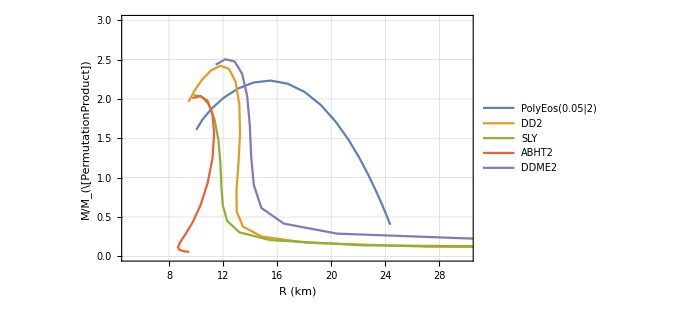

```mathematica
{First[#]["eos"]["name"],Map[x↦{x["Rs"],x["Ms"]/MSkm},#]}&/@starList;
ListLinePlot[%[[All,2]],GridLines->Automatic,FrameLabel->{"R (km)",Row[{"M/",MSsymbol}]},PlotRange->{{5,30},{0,3}},ImageSize->500,PlotLegends->Legend[%[[All,1]]]]
```

## Ibar [Fig. 6, 1303.1528]

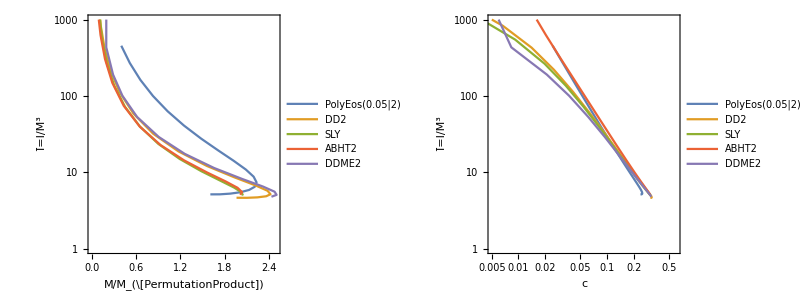

```mathematica
{First[#]["eos"]["name"],Map[x↦{x["Ms"]/MSkm,x["IbarΩ"]},#]}&/@starList;
Show[{ListLogPlot[%[[All,2]],Joined->True,PlotLegends->Legend[%[[All,1]]],GridLines->Automatic,FrameLabel->{Row[{"M/",MSsymbol}],"Ī=I/M^3"},AspectRatio->1/2,Frame->True,PlotRange->{{0,2.5},{1,10^3}}]}];

{First[#]["eos"]["name"],Map[x↦{x["c"],x["IbarΩ"]},#]}&/@starList;
Show[{ListLogLogPlot[%[[All,2]],Joined->True,PlotLegends->Legend[%[[All,1]]],GridLines->Automatic,FrameLabel->{"c","Ī=I/M^3"},AspectRatio->1/2,Frame->True,PlotRange->{{5 *10^-3,0.6},{1,10^3}}]}];
Grid[{{%%%,%}}]
```

## Qbar [Fig. 7, 1303.1528]

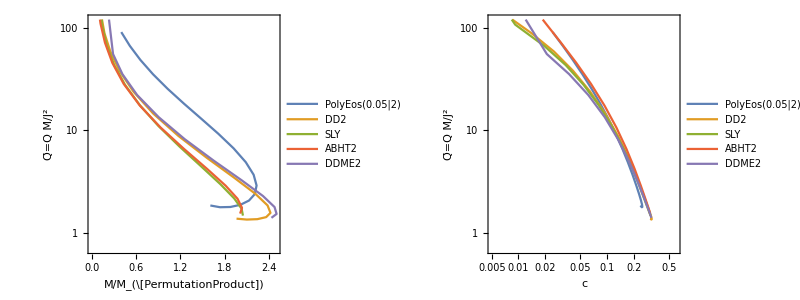

```mathematica
{First[#]["eos"]["name"],Map[x↦{x["Ms"]/MSkm,x["QbarΩ"]},#]}&/@starList;
Show[{ListLogPlot[%[[All,2]],Joined->True,PlotLegends->Legend[%[[All,1]]],GridLines->Automatic,FrameLabel->{Row[{"M/",MSsymbol}],"Q̄=Q M/J^2"},AspectRatio->1/2,Frame->True,PlotRange->{{0,2.5},{0.7,1.2*10^2}}]}];

{First[#]["eos"]["name"],Map[x↦{x["c"],x["QbarΩ"]},#]}&/@starList;
Show[{ListLogLogPlot[%[[All,2]],Joined->True,PlotLegends->Legend[%[[All,1]]],GridLines->Automatic,FrameLabel->{"c","Q̄=Q M/J^2"},AspectRatio->1/2,Frame->True,PlotRange->{{5 *10^-3,0.6},{0.7,1.2*10^2}}]}];
Grid[{{%%%,%}}]
```

## λbar [Fig. 8, 1303.1528]

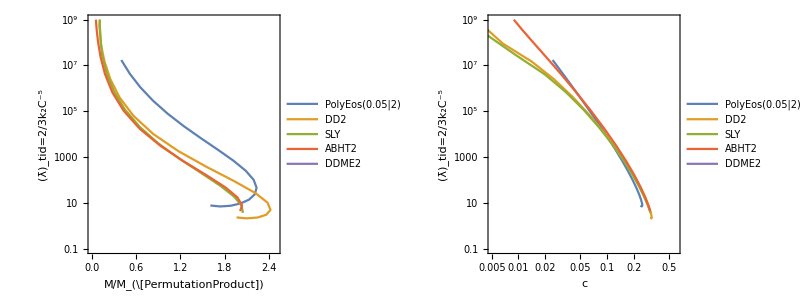

```mathematica
{First[#]["eos"]["name"],Map[x↦{x["Ms"]/MSkm,x["λbarT"]},#]}&/@starList;
Show[{ListLogPlot[%[[All,2]],Joined->True,PlotLegends->Legend[%[[All,1]]],GridLines->Automatic,FrameLabel->{Row[{"M/",MSsymbol}],"(λ̄)_tid=2/3k_2C^-5"},AspectRatio->1/2,Frame->True,PlotRange->{{0,2.5},{10^-1,10^9}}]}];

{First[#]["eos"]["name"],Map[x↦{x["c"],x["λbarT"]},#]}&/@starList;
Show[{ListLogLogPlot[%[[All,2]],Joined->True,PlotLegends->Legend[%[[All,1]]],GridLines->Automatic,FrameLabel->{"c","(λ̄)_tid=2/3k_2C^-5"},AspectRatio->1/2,Frame->True,PlotRange->{{5 *10^-3,0.6},{10^-1,10^9}}]}];
Grid[{{%%%,%}}]
```

## I-Love-Q [Fig. 9, 1303.1528]

```mathematica
{First[#]["eos"]["name"],Map[x↦{x["λbarT"],x["IbarΩ"]},#]}&/@starList;
fig9a=Show[{ListLogLogPlot[%[[All,2]],Joined->True,PlotLegends->Legend[%[[All,1]],{Left,Top}],GridLines->Automatic,FrameLabel->{"λ̄","Ī"},AspectRatio->1/2,Frame->True,PlotRange->{{10^0,10^6},{1,10^2}}],
LogLogPlot[{Ioflovefit[λ],2/5 2^(2/5)λ^(2/5)},{λ,10^-12,10^12},PlotStyle->{{Dashed,Black},Gray}]}];
```

```mathematica
{First[#]["eos"]["name"],Map[x↦{x["λbarT"],x["QbarΩ"]},#]}&/@starList;
fig9b=Show[{ListLogLogPlot[%[[All,2]],Joined->True,PlotLegends->Legend[%[[All,1]],{Right,Bottom}],GridLines->Automatic,FrameLabel->{"λ̄","Q̄"},AspectRatio->1/2,Frame->True,PlotRange->{{10^-2,10^9},{1,10^2}}],
LogLogPlot[{Qoflovefit[λ],25/(4 2^(4/5))λ^(1/5)},{λ,10^-12,10^12},PlotStyle->{{Dashed,Black},Gray}]}];
```

```mathematica
{First[#]["eos"]["name"],Map[x↦{x["QbarΩ"],x["IbarΩ"]},#]}&/@starList;
fig9c=Show[{ListLogLogPlot[%[[All,2]],Joined->True,PlotLegends->Legend[%[[All,1]],{Left,Top}],GridLines->Automatic,FrameLabel->{"Q̄","Ī"},AspectRatio->1/2,Frame->True,PlotRange->{{1,10^2},{1,10^3}}],
LogLogPlot[{IofQfit[Q],(128 Q^2)/3125},{Q,10^-2,10^6},PlotStyle->{{Dashed,Black},Gray}]}];
```

```mathematica
{First[#]["eos"]["name"],Map[x↦{x["λbarT"],x["IbarΩ"]^2 x["QbarΩ"]},#]}&/@starList;
fig9d=Show[{ListLogLogPlot[%[[All,2]],Joined->True,PlotLegends->Legend[%[[All,1]],{Left,Top}],GridLines->Automatic,FrameLabel->{"(λ̄)_tid≡λ̄","(λ̄)_rot≡Q̄ (Ī)^2"},AspectRatio->1/2,Frame->True,PlotRange->{{1,10^9},{1,10^9}}],
LogLogPlot[{Ioflovefit[λ]^2 Qoflovefit[λ],λ},{λ,10^-12,10^12},PlotStyle->{{Dashed,Black},Gray}]}];
```

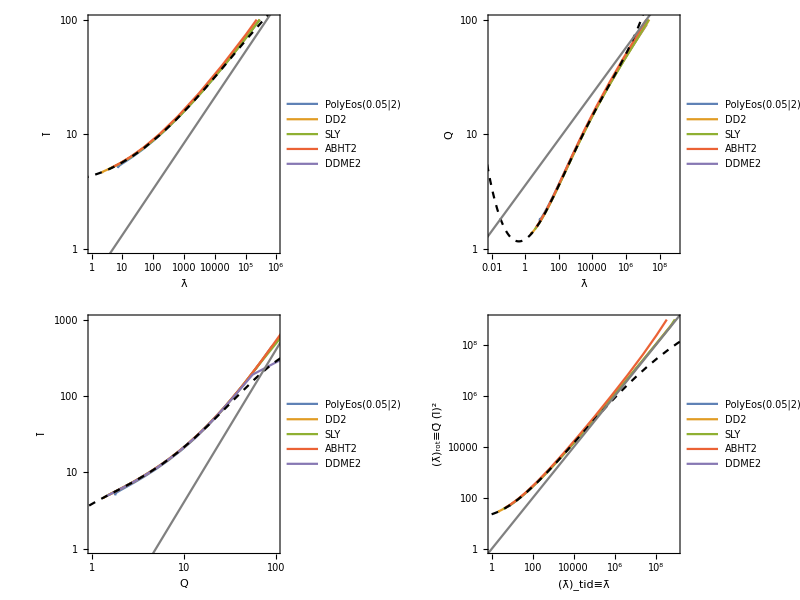

```mathematica
Grid[{{fig9a,fig9b},{fig9c,fig9d}}]
```